# Hilltop Potential

## Professor’s code with Original potential

```mathematica
Clear["Global'*"]
```

### Obtaining ϕ_sr

Considerations: - M, p are paremeters given by the potential selected.
				- ϕ_ini and ϕ_end are obteined from the calculus of 					parameters ϵ and N

```mathematica
M:=130/10^7 
p:=1.00
ϕini:=5.45315
ϕend:=0.940178
h1:=0.05
V0[p_]:=6((2p-1)/(4 p))M^2(1/(2 p))^(1/(2 p-1))
h[ϕ_]:=-1/(M (-2+3 p))3 2^((2-3 p)/(-1+2 p)) p^((1-p)/(-1+2 p)) (-1+2 p)^(3/2)  ((-1+ⅇ^(√(2/3) ϕ))^((2-3 p)/(1-2 p)) Hypergeometric2F1[1,(2-3 p)/(1-2 p),(3-5 p)/(1-2 p),((-1+ⅇ^(√(2/3) ϕ)) (-1+p))/p]-(-1+ⅇ^(√(2/3) ϕini))^((2-3 p)/(1-2 p)) Hypergeometric2F1[1,(2-3 p)/(1-2 p),(3-5 p)/(1-2 p),((-1+ⅇ^(√(2/3) ϕini)) (-1+p))/p])
```

```mathematica
root[t_]:=FindRoot[h[ϕ]-t==0,{ϕ,ϕini}]
ϕsr[t_]:=(ϕ/.First[root[t]])
ϕsrp[t_]:=(ϕsr[t+h1]-ϕsr[t])/h1
```

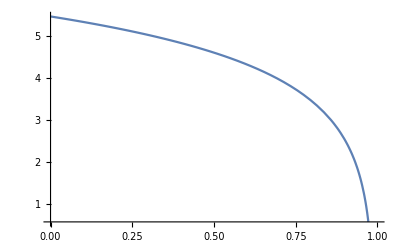

```mathematica
Plot[ϕsr[t],{t,0,1*10^7}]
```

### Obtaining ϕ(t)

```mathematica
w=NDSolve[{ϕt''[t]+3Sqrt[1/3((ϕt'[t])^2/2+ⅇ^(-2 √(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^((2 p)/(-1+2 p)) V0[p])] ϕt'[t] -2 √(2/3) ⅇ^(-2 √(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^((2 p)/(-1+2 p)) V0[p]+(2 √(2/3) ⅇ^(-√(2/3) ϕt[t]) (-1+ⅇ^(√(2/3) ϕt[t]))^(-1+(2 p)/(-1+2 p)) p V0[p])/(-1+2 p)==0,ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0]},{ϕt,ϕt',ϕt'',ϕt'''},{t,-280000,1.10 10^7}, MaxSteps->1000000,StartingStepSize->0.0001,MaxStepSize->200];
```

```mathematica
ϕ[t_]:=(ϕt/.First[w])[t];
pϕ[t_]:=(ϕt'/.First[w])[t];
ppϕ[t_]:=(ϕt''/.First[w])[t];
pppϕ[t_]:=(ϕt'''/.First[w])[t];
```

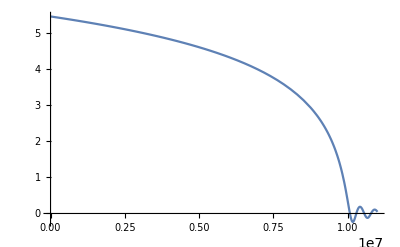

```mathematica
ϕ[t]//Plot[#,{t,0,1.1*10^7}]&
```

## Hilltop potential I

```mathematica
Clear["Global'*"]
```

### Obtaining values of ϕ_ini and ϕ_end, M and ϕsr[0]

```mathematica
V[ϕ_]:= V0 (1 - (ϕ/μ)^p);
```

```mathematica
ϵ[ϕ_]:= 1/2(V'[ϕ]/V[ϕ])^2//Expand//FullSimplify;
```

```mathematica
n :=(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p);
```

#### Fixing p = 4 we will see the behavior changing μ and M

```mathematica
p :=4.0
mulist = Range[0.01,100,0.01];
```

```mathematica
ϕend={};
Do[ϵ1 =ϵ[ϕ]==1/.{μ->i};
ϵsol =SolveValues[ϵ1,ϕ,Reals,Assumptions->ϕ>0 ];AppendTo[ϕend,{i,ϵsol[[1]]}],{i,mulist}]
```

```mathematica
ϕend
```

{{0.01,0.00152314},{0.02,0.00383703},{0.03,0.00658633},{0.04,0.0096621},{0.05,0.0130051},{0.06,0.0165771},{0.07,0.0203506},9986,{99.94,99.2403},{99.95,99.2503},{99.96,99.2603},{99.97,99.2703},{99.98,99.2803},{99.99,99.2903},{100.,99.3003}}
 |  |  |  |

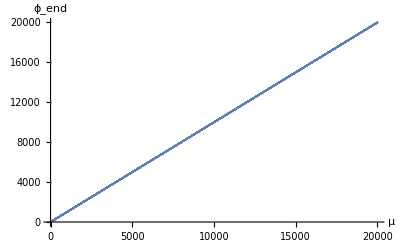

```mathematica
ϕend//ListPlot[#,AxesLabel->{"μ", "ϕ_end"}]&
```

```mathematica
n1=n-60;
ϕinilist ={};
Do[n2 =n1/.{ϕ->ϕend[[i,2]],μ->ϕend[[i,1]]}//N;
AppendTo[ϕinilist,SolveValues[n2==0,ϕi,Reals,Assumptions->ϕi>0]],{i,Length[ϕend]}]
```

```mathematica
ϕinilist
```

{{4.56433×10^-6,21.909},{0.0000182572,21.9092},{0.0000410784,21.9093},{0.0000730276,21.9095},{0.000114104,21.9097},{0.000164309,21.91},9989,{89.584,111.538},{89.5939,111.548},{89.6039,111.558},{89.6138,111.568},{89.6237,111.578}}
 |  |  |  |

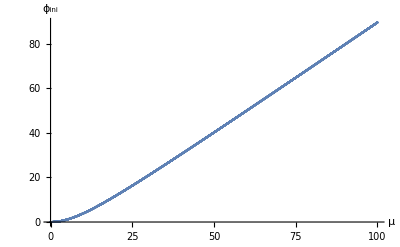

```mathematica
nsol1 =Table[{ϕend[[i,1]],ϕinilist[[i,1]]},{i,Length[ϕinilist]}];
ListPlot[nsol1,AxesLabel->{"μ", "ϕ_ini"}]
```

#### For M

```mathematica
PR := 1/(24 π^2) V[ϕ]/ϵ[ϕ]
```

```mathematica
Vini =SolveValues[PR==ΔR,V0][[1]];
M = Vini^(1/4);
```

```mathematica
ΔR := 2.2800625*10^-9
Mlist ={};
Do[AppendTo[Mlist,{ϕend[[i,1]],M/.{ϕ->ϕend[[i,2]]- ϕend[[i,2]]*0.1,μ->ϕend[[i,1]]}}],{i,Length[ϕend]}]
```

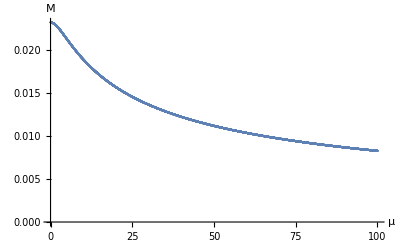

```mathematica
Mlist//ListPlot[#,AxesLabel->{"μ", "M"}]&
```

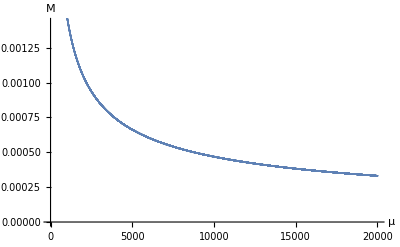

```mathematica
Mlist//ListPlot[#,AxesLabel->{"μ", "M"}]&
```

```mathematica
Mlist
```

{{0.01,0.023146},{0.02,0.0231459},{0.03,0.0231457},{0.04,0.0231455},{0.05,0.0231452},{0.06,0.023145},{0.07,0.0231447},9987,{99.95,0.0082543},{99.96,0.00825392},{99.97,0.00825355},{99.98,0.00825318},{99.99,0.0082528},{100.,0.00825243}}
 |  |  |  |

Parameters data is summarized in the following cell:  μ , ϕ_end, ϕ_ini, M

```mathematica
dataparameters = Table[{Mlist[[i,1]],ϕend[[i,2]],ϕinilist[[i,1]],Mlist[[i,2]]},{i,Length[ϕinilist]} ] ;
```

```mathematica
dataparameters
```

{{0.01,0.00152314,4.56433×10^-6,0.023146},{0.02,0.00383703,0.0000182572,0.0231459},{0.03,0.00658633,0.0000410784,0.0231457},9994,{99.98,99.2803,89.6039,0.00825318},{99.99,99.2903,89.6138,0.0082528},{100.,99.3003,89.6237,0.00825243}}
 |  |  |  |

```mathematica
SetDirectory["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Data"]
Export["Data_mu_phiend_phiini_M_Corrected.dat",dataparameters]
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Data

Data_mu_phiend_phiini_M_Corrected.dat

```mathematica
dataparameters//TableForm;
```

#### ϕ(t)

```mathematica
SetDirectory["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Data"]
dataparameters =Import["Data_mu_phiend_phiini_M.dat"];
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Data

```mathematica
g[ϕ_,μ_,ϕini_,M_]:=1/(M^4 p)√3 (-1/(M^4 (-2+p))ϕ^2 (ϕ/μ)^-p (-M^4 (-1+(ϕ/μ)^p))^(3/2) Hypergeometric2F1[1,1/2+2/p,2/p,(ϕ/μ)^p]+1/(M^4 (-2+p))ϕini^2 (ϕini/μ)^-p (-M^4 (-1+(ϕini/μ)^p))^(3/2) Hypergeometric2F1[1,1/2+2/p,2/p,(ϕini/μ)^p]);
```

```mathematica
glist = Table[{g[ϕ,dataparameters[[i,1]],dataparameters[[i,3]],dataparameters[[i,4]]]},{i,Length[dataparameters]}];
```

```mathematica
ϕsr0list={};
Do[root[t_] := FindRoot[glist[[i]]-t==0,{ϕ,dataparameters[[i,3]]}]/.i->j;
ϕsr[t_]:=(ϕ/.root[t]);AppendTo[ϕsr0list,ϕsr[0]],{j,Length[dataparameters]}]
```

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::srect: Value {{0.01,0.00152314,4.56433×10^-6,0.023146},{0.02,0.00383703,0.0000182572,0.0231459},{0.03,0.00658633,0.0000410784,0.0231457},{0.04,0.0096621,0.0000730276,0.0231455},«4»,{0.09,0.0284246,0.000369681,0.0231441},{0.1,0.0326955,0.00045639,0.0231438},«9990»}⟦i,3⟧ in search specification {ϕ,dataparameters⟦i,3⟧} is not a number or array of numbers.

Part::pkspec1: The expression i cannot be used as a part specification.

FindRoot::srect: Value {{0.01,0.00152314,4.56433×10^-6,0.023146},{0.02,0.00383703,0.0000182572,0.0231459},{0.03,0.00658633,0.0000410784,0.0231457},{0.04,0.0096621,0.0000730276,0.0231455},«4»,{0.09,0.0284246,0.000369681,0.0231441},{0.1,0.0326955,0.00045639,0.0231438},«9990»}⟦i,3⟧ in search specification {ϕ,dataparameters⟦i,3⟧} is not a number or array of numbers.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

FindRoot::srect: Value {{0.01,0.00152314,4.56433×10^-6,0.023146},{0.02,0.00383703,0.0000182572,0.0231459},{0.03,0.00658633,0.0000410784,0.0231457},{0.04,0.0096621,0.0000730276,0.0231455},«4»,{0.09,0.0284246,0.000369681,0.0231441},{0.1,0.0326955,0.00045639,0.0231438},«9990»}⟦i,3⟧ in search specification {ϕ,dataparameters⟦i,3⟧} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ϕsr0list;
```

```mathematica
dat = AppendTo[Transpose[dataparameters],ϕsr0list];
```

Set::write: Tag Transpose in Transpose[{{0.01,0.00152314,4.56433×10^-6,0.023146},{0.02,0.00383703,0.0000182572,0.0231459},{0.03,0.00658633,0.0000410784,0.0231457},{0.04,0.0096621,0.0000730276,0.0231455},«4»,{0.09,0.0284246,0.000369681,0.0231441},{0.1,0.0326955,0.00045639,0.0231438},«9990»}] is Protected.

```mathematica
datϕsr =Transpose[dat];
```

```mathematica
datϕsr
```

{{0.01,0.00152314,4.56433×10^-6,0.023146,4.56433×10^-6},{0.02,0.00383703,0.0000182572,0.0231459,0.0000182572},{0.03,0.00658633,0.0000410784,0.0231457,0.0000410784},9995,{99.99,99.2903,89.6138,0.0082528,89.6138},{100.,99.3003,89.6237,0.00825243,89.6237}}
 |  |  |  |

```mathematica
Export["Data_mu_phiend_phiini_M_g1.dat",datϕsr]
```

Data_mu_phiend_phiini_M_g1.dat

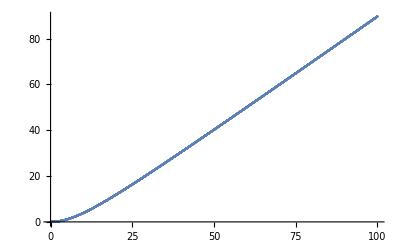

```mathematica
Table[{datϕsr[[i,1]],datϕsr[[i,5]]},{i,Length[datϕsr]}]//ListPlot
```

```mathematica
datϕsrreal ={};
Do[If[datϕsr[[i,5]]∈ Reals,AppendTo[datϕsrreal,datϕsr[[i]]]],{i,Length[datϕsr]}]
```

```mathematica
Length[datϕsrreal]
```

10000

```mathematica
Export["Data_mu_phiend_phiini_M_g1_Reals.dat",datϕsrreal]
```

Data_mu_phiend_phiini_M_g1_Reals.dat

## Analysis with data obtained before

```mathematica
SetDirectory["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Data"]
lis = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\Data\\Data_mu_phiend_phiini_M_corrected.dat"];
```

C:\Users\RAUL\Documents\Wolfram Mathematica\Titulation - Cosmology\Data

```mathematica
lis//TableForm
```

4 | 3.44314 | 22.6484 | 0.0152607 | 22.6484
12 | 11.3508 | 27.2366 | 0.0112951 | 27.2366
21 | 20.3271 | 34.6711 | 0.00916454 | 34.6711
28 | 27.3188 | 41.0506 | 0.00814272 | 41.0506
31 | 30.3164 | 43.8621 | 0.00779814 | 43.8621
43 | 42.31 | 55.3554 | 0.00675771 | 55.3554
46 | 45.3089 | 58.2681 | 0.00655659 | 58.2681
56 | 55.3061 | 68.0423 | 0.00599657 | 68.0423
57 | 56.3058 | 69.024 | 0.00594813 | 69.024
107 | 106.3 | 118.539 | 0.00442751 | 118.539
117 | 116.299 | 128.491 | 0.00424234 | 128.491
152 | 151.298 | 163.373 | 0.00374002 | 163.373
156 | 155.298 | 167.363 | 0.0036933 | 167.363
167 | 166.297 | 178.337 | 0.00357331 | 178.337
187 | 186.297 | 198.299 | 0.00338217 | 198.299
227 | 226.296 | 238.242 | 0.00307694 | 238.242
260 | 259.296 | 271.209 | 0.00287906 | 271.209
308 | 307.295 | 319.173 | 0.00264918 | 319.173
309 | 308.295 | 320.172 | 0.00264496 | 320.172
324 | 323.295 | 335.163 | 0.00258397 | 335.163
329 | 328.295 | 340.16 | 0.00256456 | 340.16
373 | 372.295 | 384.139 | 0.00241072 | 384.139
375 | 374.295 | 386.138 | 0.00240437 | 386.138
378 | 377.295 | 389.137 | 0.00239493 | 389.137
381 | 380.295 | 392.135 | 0.00238561 | 392.135
410 | 409.295 | 421.124 | 0.00230077 | 421.124
443 | 442.295 | 454.113 | 0.00221442 | 454.113
462 | 461.295 | 473.108 | 0.00216891 | 473.108
464 | 463.295 | 475.107 | 0.00216428 | 475.107
482 | 481.294 | 493.102 | 0.00212392 | 493.102
503 | 502.294 | 514.097 | 0.00207956 | 514.097
505 | 504.294 | 516.096 | 0.00207548 | 516.096
511 | 510.294 | 522.095 | 0.00206338 | 522.095
521 | 520.294 | 532.093 | 0.00204367 | 532.093
532 | 531.294 | 543.09 | 0.00202264 | 543.09
542 | 541.294 | 553.088 | 0.00200407 | 553.088
555 | 554.294 | 566.086 | 0.00198067 | 566.086
560 | 559.294 | 571.085 | 0.00197189 | 571.085
561 | 560.294 | 572.085 | 0.00197015 | 572.085
578 | 577.294 | 589.081 | 0.00194121 | 589.081
592 | 591.294 | 603.079 | 0.00191832 | 603.079
607 | 606.294 | 618.076 | 0.00189467 | 618.076
616 | 615.294 | 627.075 | 0.00188089 | 627.075
636 | 635.294 | 647.072 | 0.00185132 | 647.072
642 | 641.294 | 653.071 | 0.00184271 | 653.071
654 | 653.294 | 665.069 | 0.00182586 | 665.069
658 | 657.294 | 669.069 | 0.00182035 | 669.069
659 | 658.294 | 670.069 | 0.00181897 | 670.069
667 | 666.294 | 678.068 | 0.00180812 | 678.068
690 | 689.294 | 701.065 | 0.00177795 | 701.065
711 | 710.294 | 722.062 | 0.00175168 | 722.062
743 | 742.294 | 754.058 | 0.00171381 | 754.058
752 | 751.294 | 763.057 | 0.00170359 | 763.057
767 | 766.294 | 778.056 | 0.00168696 | 778.056
780 | 779.294 | 791.054 | 0.00167294 | 791.054
793 | 792.294 | 804.053 | 0.00165926 | 804.053
831 | 830.294 | 842.05 | 0.00162111 | 842.05
840 | 839.294 | 851.049 | 0.00161245 | 851.049
866 | 865.294 | 877.047 | 0.00158821 | 877.047
886 | 885.294 | 897.045 | 0.00157028 | 897.045
902 | 901.294 | 913.044 | 0.00155637 | 913.044
928 | 927.294 | 939.042 | 0.00153453 | 939.042
939 | 938.294 | 950.041 | 0.00152557 | 950.041
985 | 984.294 | 996.038 | 0.00148971 | 996.038
993 | 992.294 | 1004.04 | 0.00148372 | 1004.04
1000 | 999.294 | 1011.04 | 0.00147855 | 1011.04
1092 | 1091.29 | 1103.03 | 0.0014152 | 1103.03
1096 | 1095.29 | 1107.03 | 0.00141262 | 1107.03
1114 | 1113.29 | 1125.03 | 0.00140122 | 1125.03
1137 | 1136.29 | 1148.03 | 0.00138703 | 1148.03
1150 | 1149.29 | 1161.03 | 0.00137921 | 1161.03
1154 | 1153.29 | 1165.03 | 0.00137683 | 1165.03
1172 | 1171.29 | 1183.03 | 0.00136626 | 1183.03
1181 | 1180.29 | 1192.03 | 0.00136106 | 1192.03
1187 | 1186.29 | 1198.03 | 0.00135763 | 1198.03
1191 | 1190.29 | 1202.03 | 0.00135536 | 1202.03
1215 | 1214.29 | 1226.03 | 0.00134197 | 1226.03
1219 | 1218.29 | 1230.03 | 0.00133977 | 1230.03
1237 | 1236.29 | 1248.03 | 0.00133003 | 1248.03
1241 | 1240.29 | 1252.03 | 0.00132789 | 1252.03
1248 | 1247.29 | 1259.03 | 0.00132418 | 1259.03
1258 | 1257.29 | 1269.03 | 0.00131892 | 1269.03
1277 | 1276.29 | 1288.02 | 0.00130911 | 1288.02
1278 | 1277.29 | 1289.02 | 0.0013086 | 1289.02
1279 | 1278.29 | 1290.02 | 0.00130809 | 1290.02
1302 | 1301.29 | 1313.02 | 0.00129653 | 1313.02
1309 | 1308.29 | 1320.02 | 0.00129308 | 1320.02
1311 | 1310.29 | 1322.02 | 0.00129209 | 1322.02
1323 | 1322.29 | 1334.02 | 0.00128624 | 1334.02
1339 | 1338.29 | 1350.02 | 0.00127856 | 1350.02
1369 | 1368.29 | 1380.02 | 0.00126453 | 1380.02
1372 | 1371.29 | 1383.02 | 0.00126315 | 1383.02
1376 | 1375.29 | 1387.02 | 0.00126132 | 1387.02
1392 | 1391.29 | 1403.02 | 0.00125408 | 1403.02
1397 | 1396.29 | 1408.02 | 0.00125184 | 1408.02
1398 | 1397.29 | 1409.02 | 0.00125139 | 1409.02
1405 | 1404.29 | 1416.02 | 0.00124828 | 1416.02
1418 | 1417.29 | 1429.02 | 0.00124257 | 1429.02
1432 | 1431.29 | 1443.02 | 0.0012365 | 1443.02
1451 | 1450.29 | 1462.02 | 0.00122841 | 1462.02
1485 | 1484.29 | 1496.02 | 0.00121431 | 1496.02
1502 | 1501.29 | 1513.02 | 0.00120744 | 1513.02
1525 | 1524.29 | 1536.02 | 0.00119833 | 1536.02
1532 | 1531.29 | 1543.02 | 0.0011956 | 1543.02
1539 | 1538.29 | 1550.02 | 0.00119289 | 1550.02
1587 | 1586.29 | 1598.02 | 0.00117477 | 1598.02
1591 | 1590.29 | 1602.02 | 0.0011733 | 1602.02
1597 | 1596.29 | 1608.01 | 0.0011711 | 1608.01
1607 | 1606.29 | 1618.01 | 0.00116746 | 1618.01
1677 | 1676.29 | 1688.01 | 0.00114291 | 1688.01
1688 | 1687.29 | 1699.01 | 0.00113919 | 1699.01
1691 | 1690.29 | 1702.01 | 0.00113818 | 1702.01
1703 | 1702.29 | 1714.01 | 0.00113418 | 1714.01
1710 | 1709.29 | 1721.01 | 0.00113186 | 1721.01
1717 | 1716.29 | 1728.01 | 0.00112956 | 1728.01
1723 | 1722.29 | 1734.01 | 0.00112759 | 1734.01
1725 | 1724.29 | 1736.01 | 0.00112694 | 1736.01
1737 | 1736.29 | 1748.01 | 0.00112305 | 1748.01
1754 | 1753.29 | 1765.01 | 0.00111761 | 1765.01
1763 | 1762.29 | 1774.01 | 0.00111477 | 1774.01
1767 | 1766.29 | 1778.01 | 0.00111351 | 1778.01
1783 | 1782.29 | 1794.01 | 0.00110851 | 1794.01
1786 | 1785.29 | 1797.01 | 0.00110759 | 1797.01
1799 | 1798.29 | 1810.01 | 0.00110359 | 1810.01
1815 | 1814.29 | 1826.01 | 0.00109873 | 1826.01
1824 | 1823.29 | 1835.01 | 0.00109602 | 1835.01
1833 | 1832.29 | 1844.01 | 0.00109333 | 1844.01
1845 | 1844.29 | 1856.01 | 0.00108978 | 1856.01
1857 | 1856.29 | 1868.01 | 0.00108626 | 1868.01
1893 | 1892.29 | 1904.01 | 0.00107591 | 1904.01
1932 | 1931.29 | 1943.01 | 0.00106503 | 1943.01
1935 | 1934.29 | 1946.01 | 0.0010642 | 1946.01
1950 | 1949.29 | 1961.01 | 0.00106011 | 1961.01
1966 | 1965.29 | 1977.01 | 0.0010558 | 1977.01
1968 | 1967.29 | 1979.01 | 0.00105527 | 1979.01
1978 | 1977.29 | 1989.01 | 0.0010526 | 1989.01
1983 | 1982.29 | 1994.01 | 0.00105128 | 1994.01
2003 | 2002.29 | 2014.01 | 0.00104603 | 2014.01
2059 | 2058.29 | 2070.01 | 0.00103174 | 2070.01
2070 | 2069.29 | 2081.01 | 0.001029 | 2081.01
2073 | 2072.29 | 2084.01 | 0.00102826 | 2084.01
2099 | 2098.29 | 2110.01 | 0.00102189 | 2110.01
2175 | 2174.29 | 2186. | 0.00100392 | 2186.
2182 | 2181.29 | 2193. | 0.00100231 | 2193.
2189 | 2188.29 | 2200. | 0.00100071 | 2200.
2200 | 2199.29 | 2211. | 0.000998211 | 2211.
2231 | 2230.29 | 2242. | 0.000991267 | 2242.
2249 | 2248.29 | 2260. | 0.000987301 | 2260.
2276 | 2275.29 | 2287. | 0.000981441 | 2287.
2315 | 2314.29 | 2326. | 0.000973157 | 2326.
2333 | 2332.29 | 2344. | 0.000969404 | 2344.
2345 | 2344.29 | 2356. | 0.000966925 | 2356.
2360 | 2359.29 | 2371. | 0.000963854 | 2371.
2366 | 2365.29 | 2377. | 0.000962634 | 2377.
2375 | 2374.29 | 2386. | 0.000960812 | 2386.
2377 | 2376.29 | 2388. | 0.000960409 | 2388.
2388 | 2387.29 | 2399. | 0.000958199 | 2399.
2415 | 2414.29 | 2426. | 0.000952839 | 2426.
2421 | 2420.29 | 2432. | 0.00095166 | 2432.
2436 | 2435.29 | 2447. | 0.000948731 | 2447.
2438 | 2437.29 | 2449. | 0.000948343 | 2449.
2442 | 2441.29 | 2453. | 0.000947567 | 2453.
2453 | 2452.29 | 2464. | 0.000945445 | 2464.
2466 | 2465.29 | 2477. | 0.000942955 | 2477.
2475 | 2474.29 | 2486. | 0.000941242 | 2486.
2492 | 2491.29 | 2503. | 0.000938033 | 2503.
2541 | 2540.29 | 2552. | 0.000928962 | 2552.
2562 | 2561.29 | 2573. | 0.000925155 | 2573.
2563 | 2562.29 | 2574. | 0.000924975 | 2574.
2564 | 2563.29 | 2575. | 0.000924795 | 2575.
2582 | 2581.29 | 2593. | 0.000921572 | 2593.
2604 | 2603.29 | 2615. | 0.000917678 | 2615.
2610 | 2609.29 | 2621. | 0.000916625 | 2621.
2614 | 2613.29 | 2625. | 0.000915925 | 2625.
2619 | 2618.29 | 2630. | 0.000915052 | 2630.
2653 | 2652.29 | 2664. | 0.000909181 | 2664.
2681 | 2680.29 | 2692. | 0.000904429 | 2692.
2765 | 2764.29 | 2776. | 0.000890611 | 2776.
2801 | 2800.29 | 2812. | 0.000884879 | 2812.
2835 | 2834.29 | 2846. | 0.000879567 | 2846.
2856 | 2855.29 | 2867. | 0.000876333 | 2867.
2857 | 2856.29 | 2868. | 0.00087618 | 2868.
2864 | 2863.29 | 2875. | 0.00087511 | 2875.
2865 | 2864.29 | 2876. | 0.000874958 | 2876.
2869 | 2868.29 | 2880. | 0.000874349 | 2880.
2870 | 2869.29 | 2881. | 0.000874197 | 2881.
2917 | 2916.29 | 2928. | 0.000867138 | 2928.
2920 | 2919.29 | 2931. | 0.000866693 | 2931.
2927 | 2926.29 | 2938. | 0.000865658 | 2938.
2933 | 2932.29 | 2944. | 0.000864773 | 2944.
2934 | 2933.29 | 2945. | 0.000864626 | 2945.
2940 | 2939.29 | 2951. | 0.000863745 | 2951.
2950 | 2949.29 | 2961. | 0.000862282 | 2961.
2959 | 2958.29 | 2970. | 0.000860972 | 2970.
2970 | 2969.29 | 2981. | 0.000859379 | 2981.
2981 | 2980.29 | 2992. | 0.000857795 | 2992.
2985 | 2984.29 | 2996. | 0.000857221 | 2996.
2989 | 2988.29 | 3000. | 0.000856648 | 3000.
2990 | 2989.29 | 3001. | 0.000856505 | 3001.
2998 | 2997.29 | 3009. | 0.000855363 | 3009.
3013 | 3012.29 | 3024. | 0.000853235 | 3024.
3022 | 3021.29 | 3033. | 0.000851966 | 3033.
3047 | 3046.29 | 3058. | 0.000848469 | 3058.
3069 | 3068.29 | 3080. | 0.000845428 | 3080.
3070 | 3069.29 | 3081. | 0.00084529 | 3081.
3073 | 3072.29 | 3084. | 0.000844878 | 3084.
3083 | 3082.29 | 3094. | 0.000843509 | 3094.
3099 | 3098.29 | 3110. | 0.000841332 | 3110.
3101 | 3100.29 | 3112. | 0.000841061 | 3112.
3105 | 3104.29 | 3116. | 0.00084052 | 3116.
3110 | 3109.29 | 3121. | 0.000839845 | 3121.
3140 | 3139.29 | 3151. | 0.00083583 | 3151.
3150 | 3149.29 | 3161. | 0.000834505 | 3161.
3157 | 3156.29 | 3168. | 0.00083358 | 3168.
3164 | 3163.29 | 3175. | 0.000832659 | 3175.
3167 | 3166.29 | 3178. | 0.000832266 | 3178.
3172 | 3171.29 | 3183. | 0.00083161 | 3183.
3195 | 3194.29 | 3206. | 0.000828616 | 3206.
3200 | 3199.29 | 3211. | 0.00082797 | 3211.
3202 | 3201.29 | 3213. | 0.000827712 | 3213.
3206 | 3205.29 | 3217. | 0.000827196 | 3217.
3232 | 3231.29 | 3243. | 0.000823867 | 3243.
3275 | 3274.29 | 3286. | 0.000818449 | 3286.
3279 | 3278.29 | 3290. | 0.000817951 | 3290.
3300 | 3299.29 | 3311. | 0.000815348 | 3311.
3311 | 3310.29 | 3322. | 0.000813994 | 3322.
3312 | 3311.29 | 3323. | 0.000813872 | 3323.
3339 | 3338.29 | 3350. | 0.000810579 | 3350.
3341 | 3340.29 | 3352. | 0.000810337 | 3352.
3350 | 3349.29 | 3361. | 0.00080925 | 3361.
3359 | 3358.29 | 3370. | 0.000808166 | 3370.
3367 | 3366.29 | 3378. | 0.000807207 | 3378.
3380 | 3379.29 | 3391. | 0.000805656 | 3391.
3385 | 3384.29 | 3396. | 0.000805061 | 3396.
3398 | 3397.29 | 3408.99 | 0.000803522 | 3408.99
3403 | 3402.29 | 3413.99 | 0.000802932 | 3413.99
3414 | 3413.29 | 3424.99 | 0.00080164 | 3424.99
3437 | 3436.29 | 3447.99 | 0.000798957 | 3447.99
3473 | 3472.29 | 3483.99 | 0.000794811 | 3483.99
3479 | 3478.29 | 3489.99 | 0.000794127 | 3489.99
3501 | 3500.29 | 3511.99 | 0.000791631 | 3511.99
3522 | 3521.29 | 3532.99 | 0.000789271 | 3532.99
3598 | 3597.29 | 3608.99 | 0.000780903 | 3608.99
3625 | 3624.29 | 3635.99 | 0.000777993 | 3635.99
3688 | 3687.29 | 3698.99 | 0.000771329 | 3698.99
3693 | 3692.29 | 3703.99 | 0.000770807 | 3703.99
3696 | 3695.29 | 3706.99 | 0.000770495 | 3706.99
3731 | 3730.29 | 3741.99 | 0.000766877 | 3741.99
3734 | 3733.29 | 3744.99 | 0.000766569 | 3744.99
3781 | 3780.29 | 3791.99 | 0.000761796 | 3791.99
3794 | 3793.29 | 3804.99 | 0.000760492 | 3804.99
3798 | 3797.29 | 3808.99 | 0.000760092 | 3808.99
3813 | 3812.29 | 3823.99 | 0.000758597 | 3823.99
3842 | 3841.29 | 3852.99 | 0.000755733 | 3852.99
3846 | 3845.29 | 3856.99 | 0.00075534 | 3856.99
3901 | 3900.29 | 3911.99 | 0.000750003 | 3911.99
3933 | 3932.29 | 3943.99 | 0.00074695 | 3943.99
3954 | 3953.29 | 3964.99 | 0.000744966 | 3964.99
3955 | 3954.29 | 3965.99 | 0.000744872 | 3965.99
3956 | 3955.29 | 3966.99 | 0.000744778 | 3966.99
3968 | 3967.29 | 3978.99 | 0.000743653 | 3978.99
3976 | 3975.29 | 3986.99 | 0.000742905 | 3986.99
3983 | 3982.29 | 3993.99 | 0.000742253 | 3993.99
3986 | 3985.29 | 3996.99 | 0.000741974 | 3996.99
3988 | 3987.29 | 3998.99 | 0.000741788 | 3998.99
3991 | 3990.29 | 4001.99 | 0.000741509 | 4001.99
4010 | 4009.29 | 4020.99 | 0.000739753 | 4020.99
4016 | 4015.29 | 4026.99 | 0.000739201 | 4026.99
4023 | 4022.29 | 4033.99 | 0.000738558 | 4033.99
4040 | 4039.29 | 4050.99 | 0.000737005 | 4050.99
4045 | 4044.29 | 4055.99 | 0.00073655 | 4055.99
4057 | 4056.29 | 4067.99 | 0.000735461 | 4067.99
4073 | 4072.29 | 4083.99 | 0.000734017 | 4083.99
4100 | 4099.29 | 4110.99 | 0.000731599 | 4110.99
4123 | 4122.29 | 4133.99 | 0.000729558 | 4133.99
4144 | 4143.29 | 4154.99 | 0.000727709 | 4154.99
4166 | 4165.29 | 4176.99 | 0.000725787 | 4176.99
4174 | 4173.29 | 4184.99 | 0.000725092 | 4184.99
4193 | 4192.29 | 4203.99 | 0.00072345 | 4203.99
4203 | 4202.29 | 4213.99 | 0.00072259 | 4213.99
4230 | 4229.29 | 4240.99 | 0.000720283 | 4240.99
4267 | 4266.29 | 4277.99 | 0.000717157 | 4277.99
4273 | 4272.29 | 4283.99 | 0.000716654 | 4283.99
4275 | 4274.29 | 4285.99 | 0.000716486 | 4285.99
4303 | 4302.29 | 4313.99 | 0.000714154 | 4313.99
4334 | 4333.29 | 4344.99 | 0.000711598 | 4344.99
4353 | 4352.29 | 4363.99 | 0.000710045 | 4363.99
4357 | 4356.29 | 4367.99 | 0.00070972 | 4367.99
4386 | 4385.29 | 4396.99 | 0.000707372 | 4396.99
4398 | 4397.29 | 4408.99 | 0.000706408 | 4408.99
4430 | 4429.29 | 4440.99 | 0.000703855 | 4440.99
4464 | 4463.29 | 4474.99 | 0.000701172 | 4474.99
4466 | 4465.29 | 4476.99 | 0.000701015 | 4476.99
4468 | 4467.29 | 4478.99 | 0.000700859 | 4478.99
4470 | 4469.29 | 4480.99 | 0.000700702 | 4480.99
4491 | 4490.29 | 4501.99 | 0.000699064 | 4501.99
4506 | 4505.29 | 4516.99 | 0.0006979 | 4516.99
4533 | 4532.29 | 4543.99 | 0.000695821 | 4543.99
4544 | 4543.29 | 4554.99 | 0.000694979 | 4554.99
4562 | 4561.29 | 4572.99 | 0.000693608 | 4572.99
4582 | 4581.29 | 4592.99 | 0.000692095 | 4592.99
4627 | 4626.29 | 4637.99 | 0.000688725 | 4637.99
4649 | 4648.29 | 4659.99 | 0.000687095 | 4659.99
4654 | 4653.29 | 4664.99 | 0.000686726 | 4664.99
4655 | 4654.29 | 4665.99 | 0.000686652 | 4665.99
4672 | 4671.29 | 4682.99 | 0.000685403 | 4682.99
4684 | 4683.29 | 4694.99 | 0.000684526 | 4694.99
4688 | 4687.29 | 4698.99 | 0.000684234 | 4698.99
4698 | 4697.29 | 4708.99 | 0.000683506 | 4708.99
4711 | 4710.29 | 4721.99 | 0.000682564 | 4721.99
4718 | 4717.29 | 4728.99 | 0.000682058 | 4728.99
4720 | 4719.29 | 4730.99 | 0.000681913 | 4730.99
4728 | 4727.29 | 4738.99 | 0.000681337 | 4738.99
4748 | 4747.29 | 4758.99 | 0.000679902 | 4758.99
4776 | 4775.29 | 4786.99 | 0.000677908 | 4786.99
4812 | 4811.29 | 4822.99 | 0.00067537 | 4822.99
4830 | 4829.29 | 4840.99 | 0.000674112 | 4840.99
4847 | 4846.29 | 4857.99 | 0.00067293 | 4857.99
4880 | 4879.29 | 4890.99 | 0.000670653 | 4890.99
4895 | 4894.29 | 4905.99 | 0.000669626 | 4905.99
4901 | 4900.29 | 4911.99 | 0.000669216 | 4911.99
4903 | 4902.29 | 4913.99 | 0.00066908 | 4913.99
4904 | 4903.29 | 4914.99 | 0.000669011 | 4914.99
4913 | 4912.29 | 4923.99 | 0.000668399 | 4923.99
4922 | 4921.29 | 4932.99 | 0.000667788 | 4932.99
4931 | 4930.29 | 4941.99 | 0.000667179 | 4941.99
4952 | 4951.29 | 4962.99 | 0.000665765 | 4962.99
4962 | 4961.29 | 4972.99 | 0.000665094 | 4972.99
4965 | 4964.29 | 4975.99 | 0.000664893 | 4975.99
4975 | 4974.29 | 4985.99 | 0.000664225 | 4985.99
5000 | 4999.29 | 5010.99 | 0.000662564 | 5010.99
5029 | 5028.29 | 5039.99 | 0.000660653 | 5039.99
5030 | 5029.29 | 5040.99 | 0.000660588 | 5040.99
5032 | 5031.29 | 5042.99 | 0.000660456 | 5042.99
5039 | 5038.29 | 5049.99 | 0.000659998 | 5049.99
5059 | 5058.29 | 5069.99 | 0.000658693 | 5069.99
5066 | 5065.29 | 5076.99 | 0.000658239 | 5076.99
5077 | 5076.29 | 5087.99 | 0.000657526 | 5087.99
5093 | 5092.29 | 5103.99 | 0.000656493 | 5103.99
5104 | 5103.29 | 5114.99 | 0.000655786 | 5114.99
5113 | 5112.29 | 5123.99 | 0.000655209 | 5123.99
5140 | 5139.29 | 5150.99 | 0.000653488 | 5150.99
5147 | 5146.29 | 5157.99 | 0.000653044 | 5157.99
5151 | 5150.29 | 5161.99 | 0.00065279 | 5161.99
5191 | 5190.29 | 5201.99 | 0.000650273 | 5201.99
5206 | 5205.29 | 5216.99 | 0.000649336 | 5216.99
5215 | 5214.29 | 5225.99 | 0.000648776 | 5225.99
5231 | 5230.29 | 5241.99 | 0.000647784 | 5241.99
5234 | 5233.29 | 5244.99 | 0.000647599 | 5244.99
5272 | 5271.29 | 5282.99 | 0.000645263 | 5282.99
5295 | 5294.29 | 5305.99 | 0.000643861 | 5305.99
5298 | 5297.29 | 5308.99 | 0.000643679 | 5308.99
5300 | 5299.29 | 5310.99 | 0.000643558 | 5310.99
5312 | 5311.29 | 5322.99 | 0.000642831 | 5322.99
5325 | 5324.29 | 5335.99 | 0.000642047 | 5335.99
5326 | 5325.29 | 5336.99 | 0.000641987 | 5336.99
5340 | 5339.29 | 5350.99 | 0.000641145 | 5350.99
5348 | 5347.29 | 5358.99 | 0.000640666 | 5358.99
5350 | 5349.29 | 5360.99 | 0.000640546 | 5360.99
5373 | 5372.29 | 5383.99 | 0.000639175 | 5383.99
5374 | 5373.29 | 5384.99 | 0.000639116 | 5384.99
5393 | 5392.29 | 5403.99 | 0.00063799 | 5403.99
5401 | 5400.29 | 5411.99 | 0.000637518 | 5411.99
5406 | 5405.29 | 5416.99 | 0.000637223 | 5416.99
5414 | 5413.29 | 5424.99 | 0.000636753 | 5424.99
5440 | 5439.29 | 5450.99 | 0.000635231 | 5450.99
5444 | 5443.29 | 5454.99 | 0.000634997 | 5454.99
5457 | 5456.29 | 5467.99 | 0.000634241 | 5467.99
5465 | 5464.29 | 5475.99 | 0.000633777 | 5475.99
5480 | 5479.29 | 5490.99 | 0.00063291 | 5490.99
5482 | 5481.29 | 5492.99 | 0.000632795 | 5492.99
5489 | 5488.29 | 5499.99 | 0.000632392 | 5499.99
5528 | 5527.29 | 5538.99 | 0.000630159 | 5538.99
5534 | 5533.29 | 5544.99 | 0.000629818 | 5544.99
5552 | 5551.29 | 5562.99 | 0.000628797 | 5562.99
5587 | 5586.29 | 5597.99 | 0.000626826 | 5597.99
5605 | 5604.29 | 5615.99 | 0.000625819 | 5615.99
5624 | 5623.29 | 5634.99 | 0.000624762 | 5634.99
5625 | 5624.29 | 5635.99 | 0.000624707 | 5635.99
5627 | 5626.29 | 5637.99 | 0.000624596 | 5637.99
5632 | 5631.29 | 5642.99 | 0.000624319 | 5642.99
5639 | 5638.29 | 5649.99 | 0.000623932 | 5649.99
5654 | 5653.29 | 5664.99 | 0.000623104 | 5664.99
5658 | 5657.29 | 5668.99 | 0.000622884 | 5668.99
5667 | 5666.29 | 5677.99 | 0.00062239 | 5677.99
5676 | 5675.29 | 5686.99 | 0.000621896 | 5686.99
5682 | 5681.29 | 5692.99 | 0.000621568 | 5692.99
5689 | 5688.29 | 5699.99 | 0.000621186 | 5699.99
5737 | 5736.29 | 5747.99 | 0.000618584 | 5747.99
5789 | 5788.29 | 5799.99 | 0.000615802 | 5799.99
5808 | 5807.29 | 5818.99 | 0.000614795 | 5818.99
5840 | 5839.29 | 5850.99 | 0.00061311 | 5850.99
5848 | 5847.29 | 5858.99 | 0.000612691 | 5858.99
5851 | 5850.29 | 5861.99 | 0.000612534 | 5861.99
5859 | 5858.29 | 5869.99 | 0.000612116 | 5869.99
5862 | 5861.29 | 5872.99 | 0.000611959 | 5872.99
5864 | 5863.29 | 5874.99 | 0.000611855 | 5874.99
5889 | 5888.29 | 5899.99 | 0.000610556 | 5899.99
5902 | 5901.29 | 5912.99 | 0.000609884 | 5912.99
5910 | 5909.29 | 5920.99 | 0.000609471 | 5920.99
5927 | 5926.29 | 5937.99 | 0.000608597 | 5937.99
5933 | 5932.29 | 5943.99 | 0.00060829 | 5943.99
5944 | 5943.29 | 5954.99 | 0.000607727 | 5954.99
5950 | 5949.29 | 5960.99 | 0.000607421 | 5960.99
5971 | 5970.29 | 5981.99 | 0.000606353 | 5981.99
5985 | 5984.29 | 5995.99 | 0.000605644 | 5995.99
5988 | 5987.29 | 5998.99 | 0.000605492 | 5998.99
6005 | 6004.29 | 6015.99 | 0.000604635 | 6015.99
6023 | 6022.29 | 6033.99 | 0.000603732 | 6033.99
6034 | 6033.29 | 6044.99 | 0.000603182 | 6044.99
6052 | 6051.29 | 6062.99 | 0.000602285 | 6062.99
6057 | 6056.29 | 6067.99 | 0.000602036 | 6067.99
6066 | 6065.29 | 6076.99 | 0.00060159 | 6076.99
6075 | 6074.29 | 6085.99 | 0.000601144 | 6085.99
6079 | 6078.29 | 6089.99 | 0.000600947 | 6089.99
6080 | 6079.29 | 6090.99 | 0.000600897 | 6090.99
6085 | 6084.29 | 6095.99 | 0.000600651 | 6095.99
6104 | 6103.29 | 6114.99 | 0.000599716 | 6114.99
6105 | 6104.29 | 6115.99 | 0.000599667 | 6115.99
6132 | 6131.29 | 6142.99 | 0.000598346 | 6142.99
6207 | 6206.29 | 6217.99 | 0.000594723 | 6217.99
6213 | 6212.29 | 6223.99 | 0.000594436 | 6223.99
6225 | 6224.29 | 6235.99 | 0.000593864 | 6235.99
6226 | 6225.29 | 6236.99 | 0.000593816 | 6236.99
6243 | 6242.29 | 6253.99 | 0.000593008 | 6253.99
6270 | 6269.29 | 6280.99 | 0.00059173 | 6280.99
6278 | 6277.29 | 6288.99 | 0.000591354 | 6288.99
6294 | 6293.29 | 6304.99 | 0.000590602 | 6304.99
6299 | 6298.29 | 6309.99 | 0.000590368 | 6309.99
6309 | 6308.29 | 6319.99 | 0.0005899 | 6319.99
6316 | 6315.29 | 6326.99 | 0.000589573 | 6326.99
6340 | 6339.29 | 6350.99 | 0.000588457 | 6350.99
6351 | 6350.29 | 6361.99 | 0.000587948 | 6361.99
6353 | 6352.29 | 6363.99 | 0.000587855 | 6363.99
6357 | 6356.29 | 6367.99 | 0.000587671 | 6367.99
6402 | 6401.29 | 6412.99 | 0.000585603 | 6412.99
6404 | 6403.29 | 6414.99 | 0.000585512 | 6414.99
6411 | 6410.29 | 6421.99 | 0.000585192 | 6421.99
6417 | 6416.29 | 6427.99 | 0.000584919 | 6427.99
6429 | 6428.29 | 6439.99 | 0.000584373 | 6439.99
6485 | 6484.29 | 6495.99 | 0.000581847 | 6495.99
6488 | 6487.29 | 6498.99 | 0.000581712 | 6498.99
6489 | 6488.29 | 6499.99 | 0.000581667 | 6499.99
6505 | 6504.29 | 6515.99 | 0.000580952 | 6515.99
6529 | 6528.29 | 6539.99 | 0.000579884 | 6539.99
6566 | 6565.29 | 6576.99 | 0.000578249 | 6576.99
6573 | 6572.29 | 6583.99 | 0.000577941 | 6583.99
6574 | 6573.29 | 6584.99 | 0.000577898 | 6584.99
6592 | 6591.29 | 6602.99 | 0.000577109 | 6602.99
6604 | 6603.29 | 6614.99 | 0.000576584 | 6614.99
6620 | 6619.29 | 6630.99 | 0.000575888 | 6630.99
6622 | 6621.29 | 6632.99 | 0.000575801 | 6632.99
6630 | 6629.29 | 6640.99 | 0.000575454 | 6640.99
6634 | 6633.29 | 6644.99 | 0.00057528 | 6644.99
6635 | 6634.29 | 6645.99 | 0.000575237 | 6645.99
6637 | 6636.29 | 6647.99 | 0.00057515 | 6647.99
6689 | 6688.29 | 6699.99 | 0.000572912 | 6699.99
6693 | 6692.29 | 6703.99 | 0.000572741 | 6703.99
6696 | 6695.29 | 6706.99 | 0.000572613 | 6706.99
6700 | 6699.29 | 6710.99 | 0.000572442 | 6710.99
6702 | 6701.29 | 6712.99 | 0.000572357 | 6712.99
6727 | 6726.29 | 6737.99 | 0.000571293 | 6737.99
6759 | 6758.29 | 6769.99 | 0.00056994 | 6769.99
6764 | 6763.29 | 6774.99 | 0.000569729 | 6774.99
6783 | 6782.29 | 6793.99 | 0.000568931 | 6793.99
6811 | 6810.29 | 6821.99 | 0.000567762 | 6821.99
6822 | 6821.29 | 6832.99 | 0.000567304 | 6832.99
6831 | 6830.29 | 6841.99 | 0.000566931 | 6841.99
6868 | 6867.29 | 6878.99 | 0.000565403 | 6878.99
6896 | 6895.29 | 6906.99 | 0.000564254 | 6906.99
6932 | 6931.29 | 6942.99 | 0.000562788 | 6942.99
6993 | 6992.29 | 7003.99 | 0.00056033 | 7003.99
7021 | 7020.29 | 7031.99 | 0.000559213 | 7031.99
7029 | 7028.29 | 7039.99 | 0.000558894 | 7039.99
7062 | 7061.29 | 7072.99 | 0.000557588 | 7072.99
7066 | 7065.29 | 7076.99 | 0.00055743 | 7076.99
7077 | 7076.29 | 7087.99 | 0.000556997 | 7087.99
7122 | 7121.29 | 7132.99 | 0.000555236 | 7132.99
7128 | 7127.29 | 7138.99 | 0.000555002 | 7138.99
7132 | 7131.29 | 7142.99 | 0.000554847 | 7142.99
7156 | 7155.29 | 7166.99 | 0.000553916 | 7166.99
7160 | 7159.29 | 7170.99 | 0.000553762 | 7170.99
7170 | 7169.29 | 7180.99 | 0.000553376 | 7180.99
7243 | 7242.29 | 7253.99 | 0.000550582 | 7253.99
7244 | 7243.29 | 7254.99 | 0.000550544 | 7254.99
7284 | 7283.29 | 7294.99 | 0.000549031 | 7294.99
7302 | 7301.29 | 7312.99 | 0.000548355 | 7312.99
7304 | 7303.29 | 7314.99 | 0.00054828 | 7314.99
7305 | 7304.29 | 7315.99 | 0.000548242 | 7315.99
7313 | 7312.29 | 7323.99 | 0.000547942 | 7323.99
7329 | 7328.29 | 7339.99 | 0.000547344 | 7339.99
7355 | 7354.29 | 7365.99 | 0.000546377 | 7365.99
7363 | 7362.29 | 7373.99 | 0.00054608 | 7373.99
7365 | 7364.29 | 7375.99 | 0.000546006 | 7375.99
7366 | 7365.29 | 7376.99 | 0.000545969 | 7376.99
7416 | 7415.29 | 7426.99 | 0.000544126 | 7426.99
7430 | 7429.29 | 7440.99 | 0.000543614 | 7440.99
7453 | 7452.29 | 7463.99 | 0.000542775 | 7463.99
7516 | 7515.29 | 7526.99 | 0.000540497 | 7526.99
7517 | 7516.29 | 7527.99 | 0.000540461 | 7527.99
7519 | 7518.29 | 7529.99 | 0.000540389 | 7529.99
7543 | 7542.29 | 7553.99 | 0.000539529 | 7553.99
7552 | 7551.29 | 7562.99 | 0.000539208 | 7562.99
7564 | 7563.29 | 7574.99 | 0.00053878 | 7574.99
7580 | 7579.29 | 7590.99 | 0.000538212 | 7590.99
7585 | 7584.29 | 7595.99 | 0.000538035 | 7595.99
7600 | 7599.29 | 7610.99 | 0.000537504 | 7610.99
7680 | 7679.29 | 7690.99 | 0.000534699 | 7690.99
7690 | 7689.29 | 7700.99 | 0.000534351 | 7700.99
7707 | 7706.29 | 7717.99 | 0.000533762 | 7717.99
7710 | 7709.29 | 7720.99 | 0.000533658 | 7720.99
7717 | 7716.29 | 7727.99 | 0.000533416 | 7727.99
7734 | 7733.29 | 7744.99 | 0.00053283 | 7744.99
7735 | 7734.29 | 7745.99 | 0.000532796 | 7745.99
7741 | 7740.29 | 7751.99 | 0.000532589 | 7751.99
7743 | 7742.29 | 7753.99 | 0.000532521 | 7753.99
7792 | 7791.29 | 7802.98 | 0.000530845 | 7802.98
7799 | 7798.29 | 7809.98 | 0.000530606 | 7809.98
7857 | 7856.29 | 7867.98 | 0.000528646 | 7867.98
7860 | 7859.29 | 7870.98 | 0.000528545 | 7870.98
7872 | 7871.29 | 7882.98 | 0.000528142 | 7882.98
7874 | 7873.29 | 7884.98 | 0.000528075 | 7884.98
7931 | 7930.29 | 7941.98 | 0.000526175 | 7941.98
7964 | 7963.29 | 7974.98 | 0.000525085 | 7974.98
7977 | 7976.29 | 7987.98 | 0.000524657 | 7987.98
8005 | 8004.29 | 8015.98 | 0.000523739 | 8015.98
8018 | 8017.29 | 8028.98 | 0.000523315 | 8028.98
8039 | 8038.29 | 8049.98 | 0.000522631 | 8049.98
8051 | 8050.29 | 8061.98 | 0.000522242 | 8061.98
8053 | 8052.29 | 8063.98 | 0.000522177 | 8063.98
8117 | 8116.29 | 8127.98 | 0.000520115 | 8127.98
8122 | 8121.29 | 8132.98 | 0.000519955 | 8132.98
8129 | 8128.29 | 8139.98 | 0.000519732 | 8139.98
8134 | 8133.29 | 8144.98 | 0.000519572 | 8144.98
8151 | 8150.29 | 8161.98 | 0.00051903 | 8161.98
8153 | 8152.29 | 8163.98 | 0.000518967 | 8163.98
8185 | 8184.29 | 8195.98 | 0.000517952 | 8195.98
8214 | 8213.29 | 8224.98 | 0.000517037 | 8224.98
8217 | 8216.29 | 8227.98 | 0.000516943 | 8227.98
8234 | 8233.29 | 8244.98 | 0.000516409 | 8244.98
8258 | 8257.29 | 8268.98 | 0.000515659 | 8268.98
8277 | 8276.29 | 8287.98 | 0.000515067 | 8287.98
8300 | 8299.29 | 8310.98 | 0.000514353 | 8310.98
8351 | 8350.29 | 8361.98 | 0.000512781 | 8361.98
8367 | 8366.29 | 8377.98 | 0.000512291 | 8377.98
8386 | 8385.29 | 8396.98 | 0.000511711 | 8396.98
8403 | 8402.29 | 8413.98 | 0.000511193 | 8413.98
8432 | 8431.29 | 8442.98 | 0.000510314 | 8442.98
8445 | 8444.29 | 8455.98 | 0.000509921 | 8455.98
8447 | 8446.29 | 8457.98 | 0.000509861 | 8457.98
8459 | 8458.29 | 8469.98 | 0.000509499 | 8469.98
8488 | 8487.29 | 8498.98 | 0.000508629 | 8498.98
8503 | 8502.29 | 8513.98 | 0.00050818 | 8513.98
8524 | 8523.29 | 8534.98 | 0.000507554 | 8534.98
8576 | 8575.29 | 8586.98 | 0.000506014 | 8586.98
8580 | 8579.29 | 8590.98 | 0.000505896 | 8590.98
8582 | 8581.29 | 8592.98 | 0.000505837 | 8592.98
8614 | 8613.29 | 8624.98 | 0.000504897 | 8624.98
8692 | 8691.29 | 8702.98 | 0.000502628 | 8702.98
8754 | 8753.29 | 8764.98 | 0.000500846 | 8764.98
8785 | 8784.29 | 8795.98 | 0.000499962 | 8795.98
8791 | 8790.29 | 8801.98 | 0.000499791 | 8801.98
8796 | 8795.29 | 8806.98 | 0.000499649 | 8806.98
8861 | 8860.29 | 8871.98 | 0.000497814 | 8871.98
8891 | 8890.29 | 8901.98 | 0.000496974 | 8901.98
8896 | 8895.29 | 8906.98 | 0.000496835 | 8906.98
8899 | 8898.29 | 8909.98 | 0.000496751 | 8909.98
8931 | 8930.29 | 8941.98 | 0.000495861 | 8941.98
9021 | 9020.29 | 9031.98 | 0.000493382 | 9031.98
9032 | 9031.29 | 9042.98 | 0.000493082 | 9042.98
9068 | 9067.29 | 9078.98 | 0.000492103 | 9078.98
9111 | 9110.29 | 9121.98 | 0.000490941 | 9121.98
9136 | 9135.29 | 9146.98 | 0.000490269 | 9146.98
9137 | 9136.29 | 9147.98 | 0.000490242 | 9147.98
9146 | 9145.29 | 9156.98 | 0.000490001 | 9156.98
9169 | 9168.29 | 9179.98 | 0.000489387 | 9179.98
9216 | 9215.29 | 9226.98 | 0.000488138 | 9226.98
9233 | 9232.29 | 9243.98 | 0.000487688 | 9243.98
9246 | 9245.29 | 9256.98 | 0.000487346 | 9256.98
9257 | 9256.29 | 9267.98 | 0.000487056 | 9267.98
9258 | 9257.29 | 9268.98 | 0.00048703 | 9268.98
9290 | 9289.29 | 9300.98 | 0.000486191 | 9300.98
9298 | 9297.29 | 9308.98 | 0.000485982 | 9308.98
9302 | 9301.29 | 9312.98 | 0.000485877 | 9312.98
9311 | 9310.29 | 9321.98 | 0.000485643 | 9321.98
9330 | 9329.29 | 9340.98 | 0.000485148 | 9340.98
9334 | 9333.29 | 9344.98 | 0.000485044 | 9344.98
9339 | 9338.29 | 9349.98 | 0.000484914 | 9349.98
9342 | 9341.29 | 9352.98 | 0.000484837 | 9352.98
9343 | 9342.29 | 9353.98 | 0.000484811 | 9353.98
9344 | 9343.29 | 9354.98 | 0.000484785 | 9354.98
9346 | 9345.29 | 9356.98 | 0.000484733 | 9356.98
9348 | 9347.29 | 9358.98 | 0.000484681 | 9358.98
9354 | 9353.29 | 9364.98 | 0.000484526 | 9364.98
9372 | 9371.29 | 9382.98 | 0.00048406 | 9382.98
9385 | 9384.29 | 9395.98 | 0.000483725 | 9395.98
9389 | 9388.29 | 9399.98 | 0.000483622 | 9399.98
9403 | 9402.29 | 9413.98 | 0.000483262 | 9413.98
9418 | 9417.29 | 9428.98 | 0.000482877 | 9428.98
9429 | 9428.29 | 9439.98 | 0.000482596 | 9439.98
9438 | 9437.29 | 9448.98 | 0.000482366 | 9448.98
9447 | 9446.29 | 9457.98 | 0.000482136 | 9457.98
9459 | 9458.29 | 9469.98 | 0.00048183 | 9469.98
9460 | 9459.29 | 9470.98 | 0.000481805 | 9470.98
9467 | 9466.29 | 9477.98 | 0.000481627 | 9477.98
9471 | 9470.29 | 9481.98 | 0.000481525 | 9481.98
9474 | 9473.29 | 9484.98 | 0.000481449 | 9484.98
9484 | 9483.29 | 9494.98 | 0.000481195 | 9494.98
9509 | 9508.29 | 9519.98 | 0.000480563 | 9519.98
9528 | 9527.29 | 9538.98 | 0.000480083 | 9538.98
9538 | 9537.29 | 9548.98 | 0.000479832 | 9548.98
9578 | 9577.29 | 9588.98 | 0.000478829 | 9588.98
9581 | 9580.29 | 9591.98 | 0.000478754 | 9591.98
9598 | 9597.29 | 9608.98 | 0.00047833 | 9608.98
9601 | 9600.29 | 9611.98 | 0.000478256 | 9611.98
9635 | 9634.29 | 9645.98 | 0.000477412 | 9645.98
9658 | 9657.29 | 9668.98 | 0.000476843 | 9668.98
9670 | 9669.29 | 9680.98 | 0.000476547 | 9680.98
9672 | 9671.29 | 9682.98 | 0.000476498 | 9682.98
9690 | 9689.29 | 9700.98 | 0.000476056 | 9700.98
9697 | 9696.29 | 9707.98 | 0.000475884 | 9707.98
9717 | 9716.29 | 9727.98 | 0.000475394 | 9727.98
9721 | 9720.29 | 9731.98 | 0.000475296 | 9731.98
9736 | 9735.29 | 9746.98 | 0.00047493 | 9746.98
9738 | 9737.29 | 9748.98 | 0.000474881 | 9748.98
9748 | 9747.29 | 9758.98 | 0.000474638 | 9758.98
9754 | 9753.29 | 9764.98 | 0.000474492 | 9764.98
9799 | 9798.29 | 9809.98 | 0.000473402 | 9809.98
9810 | 9809.29 | 9820.98 | 0.000473136 | 9820.98
9812 | 9811.29 | 9822.98 | 0.000473088 | 9822.98
9831 | 9830.29 | 9841.98 | 0.000472631 | 9841.98
9859 | 9858.29 | 9869.98 | 0.00047196 | 9869.98
9866 | 9865.29 | 9876.98 | 0.000471792 | 9876.98
9868 | 9867.29 | 9878.98 | 0.000471745 | 9878.98
9871 | 9870.29 | 9881.98 | 0.000471673 | 9881.98
9882 | 9881.29 | 9892.98 | 0.000471411 | 9892.98
9896 | 9895.29 | 9906.98 | 0.000471077 | 9906.98
9917 | 9916.29 | 9927.98 | 0.000470578 | 9927.98
9920 | 9919.29 | 9930.98 | 0.000470507 | 9930.98
9922 | 9921.29 | 9932.98 | 0.00047046 | 9932.98
9925 | 9924.29 | 9935.98 | 0.000470389 | 9935.98
9937 | 9936.29 | 9947.98 | 0.000470105 | 9947.98
9955 | 9954.29 | 9965.98 | 0.00046968 | 9965.98
9968 | 9967.29 | 9978.98 | 0.000469374 | 9978.98
9985 | 9984.29 | 9995.98 | 0.000468974 | 9995.98
9993 | 9992.29 | 10004. | 0.000468786 | 10004.
9999 | 9998.29 | 10010. | 0.000468646 | 10010.
10007 | 10006.3 | 10018. | 0.000468459 | 10018.
10022 | 10021.3 | 10033. | 0.000468108 | 10033.
10052 | 10051.3 | 10063. | 0.000467409 | 10063.
10069 | 10068.3 | 10080. | 0.000467015 | 10080.
10089 | 10088.3 | 10100. | 0.000466552 | 10100.
10093 | 10092.3 | 10104. | 0.000466459 | 10104.
10105 | 10104.3 | 10116. | 0.000466183 | 10116.
10131 | 10130.3 | 10142. | 0.000465584 | 10142.
10132 | 10131.3 | 10143. | 0.000465561 | 10143.
10135 | 10134.3 | 10146. | 0.000465492 | 10146.
10137 | 10136.3 | 10148. | 0.000465446 | 10148.
10157 | 10156.3 | 10168. | 0.000464988 | 10168.
10162 | 10161.3 | 10173. | 0.000464874 | 10173.
10165 | 10164.3 | 10176. | 0.000464805 | 10176.
10176 | 10175.3 | 10187. | 0.000464554 | 10187.
10192 | 10191.3 | 10203. | 0.00046419 | 10203.
10193 | 10192.3 | 10204. | 0.000464167 | 10204.
10200 | 10199.3 | 10211. | 0.000464008 | 10211.
10204 | 10203.3 | 10215. | 0.000463917 | 10215.
10212 | 10211.3 | 10223. | 0.000463735 | 10223.
10215 | 10214.3 | 10226. | 0.000463667 | 10226.
10226 | 10225.3 | 10237. | 0.000463418 | 10237.
10250 | 10249.3 | 10261. | 0.000462875 | 10261.
10255 | 10254.3 | 10266. | 0.000462762 | 10266.
10272 | 10271.3 | 10283. | 0.000462379 | 10283.
10275 | 10274.3 | 10286. | 0.000462312 | 10286.
10306 | 10305.3 | 10317. | 0.000461616 | 10317.
10314 | 10313.3 | 10325. | 0.000461437 | 10325.
10340 | 10339.3 | 10351. | 0.000460857 | 10351.
10352 | 10351.3 | 10363. | 0.00046059 | 10363.
10363 | 10362.3 | 10374. | 0.000460346 | 10374.
10377 | 10376.3 | 10388. | 0.000460035 | 10388.
10412 | 10411.3 | 10423. | 0.000459262 | 10423.
10415 | 10414.3 | 10426. | 0.000459196 | 10426.
10421 | 10420.3 | 10432. | 0.000459063 | 10432.
10422 | 10421.3 | 10433. | 0.000459041 | 10433.
10427 | 10426.3 | 10438. | 0.000458931 | 10438.
10429 | 10428.3 | 10440. | 0.000458887 | 10440.
10430 | 10429.3 | 10441. | 0.000458865 | 10441.
10434 | 10433.3 | 10445. | 0.000458778 | 10445.
10435 | 10434.3 | 10446. | 0.000458756 | 10446.
10474 | 10473.3 | 10485. | 0.000457901 | 10485.
10483 | 10482.3 | 10494. | 0.000457705 | 10494.
10486 | 10485.3 | 10497. | 0.000457639 | 10497.
10491 | 10490.3 | 10502. | 0.00045753 | 10502.
10493 | 10492.3 | 10504. | 0.000457487 | 10504.
10495 | 10494.3 | 10506. | 0.000457443 | 10506.
10501 | 10500.3 | 10512. | 0.000457312 | 10512.
10506 | 10505.3 | 10517. | 0.000457204 | 10517.
10508 | 10507.3 | 10519. | 0.00045716 | 10519.
10509 | 10508.3 | 10520. | 0.000457138 | 10520.
10529 | 10528.3 | 10540. | 0.000456704 | 10540.
10546 | 10545.3 | 10557. | 0.000456336 | 10557.
10560 | 10559.3 | 10571. | 0.000456034 | 10571.
10617 | 10616.3 | 10628. | 0.000454808 | 10628.
10622 | 10621.3 | 10633. | 0.000454701 | 10633.
10656 | 10655.3 | 10667. | 0.000453976 | 10667.
10657 | 10656.3 | 10668. | 0.000453954 | 10668.
10675 | 10674.3 | 10686. | 0.000453572 | 10686.
10677 | 10676.3 | 10688. | 0.000453529 | 10688.
10687 | 10686.3 | 10698. | 0.000453317 | 10698.
10738 | 10737.3 | 10749. | 0.00045224 | 10749.
10763 | 10762.3 | 10774. | 0.000451715 | 10774.
10767 | 10766.3 | 10778. | 0.000451631 | 10778.
10771 | 10770.3 | 10782. | 0.000451547 | 10782.
10785 | 10784.3 | 10796. | 0.000451254 | 10796.
10801 | 10800.3 | 10812. | 0.00045092 | 10812.
10814 | 10813.3 | 10825. | 0.000450649 | 10825.
10821 | 10820.3 | 10832. | 0.000450503 | 10832.
10845 | 10844.3 | 10856. | 0.000450004 | 10856.
10849 | 10848.3 | 10860. | 0.000449922 | 10860.
10865 | 10864.3 | 10876. | 0.00044959 | 10876.
10884 | 10883.3 | 10895. | 0.000449198 | 10895.
10888 | 10887.3 | 10899. | 0.000449115 | 10899.
10911 | 10910.3 | 10922. | 0.000448642 | 10922.
10914 | 10913.3 | 10925. | 0.00044858 | 10925.
10926 | 10925.3 | 10937. | 0.000448334 | 10937.
10937 | 10936.3 | 10948. | 0.000448109 | 10948.
10938 | 10937.3 | 10949. | 0.000448088 | 10949.
10939 | 10938.3 | 10950. | 0.000448068 | 10950.
10952 | 10951.3 | 10963. | 0.000447802 | 10963.
10972 | 10971.3 | 10983. | 0.000447394 | 10983.
10983 | 10982.3 | 10994. | 0.00044717 | 10994.
10985 | 10984.3 | 10996. | 0.000447129 | 10996.
10990 | 10989.3 | 11001. | 0.000447027 | 11001.
11005 | 11004.3 | 11016. | 0.000446723 | 11016.
11016 | 11015.3 | 11027. | 0.0004465 | 11027.
11057 | 11056.3 | 11068. | 0.000445671 | 11068.
11090 | 11089.3 | 11101. | 0.000445008 | 11101.
11094 | 11093.3 | 11105. | 0.000444928 | 11105.
11096 | 11095.3 | 11107. | 0.000444888 | 11107.
11146 | 11145.3 | 11157. | 0.000443889 | 11157.
11156 | 11155.3 | 11167. | 0.000443691 | 11167.
11181 | 11180.3 | 11192. | 0.000443194 | 11192.
11189 | 11188.3 | 11200. | 0.000443036 | 11200.
11201 | 11200.3 | 11212. | 0.000442799 | 11212.
11230 | 11229.3 | 11241. | 0.000442227 | 11241.
11232 | 11231.3 | 11243. | 0.000442188 | 11243.
11239 | 11238.3 | 11250. | 0.00044205 | 11250.
11248 | 11247.3 | 11259. | 0.000441873 | 11259.
11252 | 11251.3 | 11263. | 0.000441795 | 11263.
11257 | 11256.3 | 11268. | 0.000441696 | 11268.
11265 | 11264.3 | 11276. | 0.00044154 | 11276.
11277 | 11276.3 | 11288. | 0.000441305 | 11288.
11282 | 11281.3 | 11293. | 0.000441207 | 11293.
11310 | 11309.3 | 11321. | 0.000440661 | 11321.
11358 | 11357.3 | 11369. | 0.000439729 | 11369.
11360 | 11359.3 | 11371. | 0.00043969 | 11371.
11370 | 11369.3 | 11381. | 0.000439497 | 11381.
11374 | 11373.3 | 11385. | 0.00043942 | 11385.
11379 | 11378.3 | 11390. | 0.000439323 | 11390.
11400 | 11399.3 | 11411. | 0.000438919 | 11411.
11444 | 11443.3 | 11455. | 0.000438074 | 11455.
11456 | 11455.3 | 11467. | 0.000437845 | 11467.
11467 | 11466.3 | 11478. | 0.000437635 | 11478.
11473 | 11472.3 | 11484. | 0.000437521 | 11484.
11477 | 11476.3 | 11488. | 0.000437445 | 11488.
11483 | 11482.3 | 11494. | 0.00043733 | 11494.
11510 | 11509.3 | 11521. | 0.000436817 | 11521.
11525 | 11524.3 | 11536. | 0.000436533 | 11536.
11529 | 11528.3 | 11540. | 0.000436457 | 11540.
11545 | 11544.3 | 11556. | 0.000436155 | 11556.
11565 | 11564.3 | 11576. | 0.000435778 | 11576.
11596 | 11595.3 | 11607. | 0.000435195 | 11607.
11632 | 11631.3 | 11643. | 0.000434521 | 11643.
11656 | 11655.3 | 11667. | 0.000434074 | 11667.
11657 | 11656.3 | 11668. | 0.000434055 | 11668.
11669 | 11668.3 | 11680. | 0.000433832 | 11680.
11679 | 11678.3 | 11690. | 0.000433647 | 11690.
11684 | 11683.3 | 11695. | 0.000433554 | 11695.
11688 | 11687.3 | 11699. | 0.00043348 | 11699.
11689 | 11688.3 | 11700. | 0.000433461 | 11700.
11693 | 11692.3 | 11704. | 0.000433387 | 11704.
11699 | 11698.3 | 11710. | 0.000433276 | 11710.
11717 | 11716.3 | 11728. | 0.000432943 | 11728.
11719 | 11718.3 | 11730. | 0.000432906 | 11730.
11725 | 11724.3 | 11736. | 0.000432796 | 11736.
11736 | 11735.3 | 11747. | 0.000432593 | 11747.
11744 | 11743.3 | 11755. | 0.000432445 | 11755.
11756 | 11755.3 | 11767. | 0.000432225 | 11767.
11844 | 11843.3 | 11855. | 0.000430617 | 11855.
11846 | 11845.3 | 11857. | 0.00043058 | 11857.
11858 | 11857.3 | 11869. | 0.000430363 | 11869.
11861 | 11860.3 | 11872. | 0.000430308 | 11872.
11867 | 11866.3 | 11878. | 0.000430199 | 11878.
11874 | 11873.3 | 11885. | 0.000430073 | 11885.
11880 | 11879.3 | 11891. | 0.000429964 | 11891.
11894 | 11893.3 | 11905. | 0.000429711 | 11905.
11912 | 11911.3 | 11923. | 0.000429386 | 11923.
11916 | 11915.3 | 11927. | 0.000429314 | 11927.
11934 | 11933.3 | 11945. | 0.000428991 | 11945.
11939 | 11938.3 | 11950. | 0.000428901 | 11950.
11941 | 11940.3 | 11952. | 0.000428865 | 11952.
11943 | 11942.3 | 11954. | 0.000428829 | 11954.
11948 | 11947.3 | 11959. | 0.000428739 | 11959.
11950 | 11949.3 | 11961. | 0.000428703 | 11961.
11977 | 11976.3 | 11988. | 0.00042822 | 11988.
11987 | 11986.3 | 11998. | 0.000428042 | 11998.
12017 | 12016.3 | 12028. | 0.000427507 | 12028.
12019 | 12018.3 | 12030. | 0.000427472 | 12030.
12035 | 12034.3 | 12046. | 0.000427188 | 12046.
12041 | 12040.3 | 12052. | 0.000427081 | 12052.
12061 | 12060.3 | 12072. | 0.000426727 | 12072.
12066 | 12065.3 | 12077. | 0.000426639 | 12077.
12071 | 12070.3 | 12082. | 0.00042655 | 12082.
12103 | 12102.3 | 12114. | 0.000425986 | 12114.
12108 | 12107.3 | 12119. | 0.000425898 | 12119.
12111 | 12110.3 | 12122. | 0.000425846 | 12122.
12122 | 12121.3 | 12133. | 0.000425652 | 12133.
12123 | 12122.3 | 12134. | 0.000425635 | 12134.
12125 | 12124.3 | 12136. | 0.0004256 | 12136.
12131 | 12130.3 | 12142. | 0.000425495 | 12142.
12145 | 12144.3 | 12156. | 0.000425249 | 12156.
12156 | 12155.3 | 12167. | 0.000425057 | 12167.
12172 | 12171.3 | 12183. | 0.000424778 | 12183.
12176 | 12175.3 | 12187. | 0.000424708 | 12187.
12207 | 12206.3 | 12218. | 0.000424168 | 12218.
12241 | 12240.3 | 12252. | 0.000423579 | 12252.
12244 | 12243.3 | 12255. | 0.000423527 | 12255.
12252 | 12251.3 | 12263. | 0.000423389 | 12263.
12266 | 12265.3 | 12277. | 0.000423148 | 12277.
12278 | 12277.3 | 12289. | 0.000422941 | 12289.
12290 | 12289.3 | 12301. | 0.000422734 | 12301.
12345 | 12344.3 | 12356. | 0.000421792 | 12356.
12401 | 12400.3 | 12412. | 0.000420839 | 12412.
12405 | 12404.3 | 12416. | 0.000420771 | 12416.
12414 | 12413.3 | 12425. | 0.000420619 | 12425.
12447 | 12446.3 | 12458. | 0.000420061 | 12458.
12455 | 12454.3 | 12466. | 0.000419926 | 12466.
12479 | 12478.3 | 12490. | 0.000419522 | 12490.
12487 | 12486.3 | 12498. | 0.000419388 | 12498.
12495 | 12494.3 | 12506. | 0.000419254 | 12506.
12513 | 12512.3 | 12524. | 0.000418952 | 12524.
12524 | 12523.3 | 12535. | 0.000418768 | 12535.
12533 | 12532.3 | 12544. | 0.000418618 | 12544.
12538 | 12537.3 | 12549. | 0.000418534 | 12549.
12540 | 12539.3 | 12551. | 0.000418501 | 12551.
12547 | 12546.3 | 12558. | 0.000418384 | 12558.
12553 | 12552.3 | 12564. | 0.000418284 | 12564.
12566 | 12565.3 | 12577. | 0.000418068 | 12577.
12568 | 12567.3 | 12579. | 0.000418035 | 12579.
12570 | 12569.3 | 12581. | 0.000418002 | 12581.
12596 | 12595.3 | 12607. | 0.00041757 | 12607.
12600 | 12599.3 | 12611. | 0.000417504 | 12611.
12603 | 12602.3 | 12614. | 0.000417454 | 12614.
12626 | 12625.3 | 12637. | 0.000417074 | 12637.
12647 | 12646.3 | 12658. | 0.000416728 | 12658.
12663 | 12662.3 | 12674. | 0.000416464 | 12674.
12666 | 12665.3 | 12677. | 0.000416415 | 12677.
12724 | 12723.3 | 12735. | 0.000415465 | 12735.
12735 | 12734.3 | 12746. | 0.000415286 | 12746.
12736 | 12735.3 | 12747. | 0.00041527 | 12747.
12779 | 12778.3 | 12790. | 0.000414571 | 12790.
12806 | 12805.3 | 12817. | 0.000414133 | 12817.
12813 | 12812.3 | 12824. | 0.00041402 | 12824.
12853 | 12852.3 | 12864. | 0.000413376 | 12864.
12875 | 12874.3 | 12886. | 0.000413023 | 12886.
12877 | 12876.3 | 12888. | 0.000412991 | 12888.
12886 | 12885.3 | 12897. | 0.000412846 | 12897.
12900 | 12899.3 | 12911. | 0.000412622 | 12911.
12906 | 12905.3 | 12917. | 0.000412527 | 12917.
12907 | 12906.3 | 12918. | 0.000412511 | 12918.
12912 | 12911.3 | 12923. | 0.000412431 | 12923.
12934 | 12933.3 | 12945. | 0.00041208 | 12945.
12965 | 12964.3 | 12976. | 0.000411587 | 12976.
12972 | 12971.3 | 12983. | 0.000411476 | 12983.
12974 | 12973.3 | 12985. | 0.000411444 | 12985.
12976 | 12975.3 | 12987. | 0.000411413 | 12987.
12989 | 12988.3 | 13000. | 0.000411207 | 13000.
13012 | 13011.3 | 13023. | 0.000410844 | 13023.
13035 | 13034.3 | 13046. | 0.000410481 | 13046.
13039 | 13038.3 | 13050. | 0.000410418 | 13050.
13052 | 13051.3 | 13063. | 0.000410214 | 13063.
13073 | 13072.3 | 13084. | 0.000409884 | 13084.
13076 | 13075.3 | 13087. | 0.000409837 | 13087.
13111 | 13110.3 | 13122. | 0.00040929 | 13122.
13125 | 13124.3 | 13136. | 0.000409072 | 13136.
13150 | 13149.3 | 13161. | 0.000408683 | 13161.
13177 | 13176.3 | 13188. | 0.000408264 | 13188.
13184 | 13183.3 | 13195. | 0.000408156 | 13195.
13192 | 13191.3 | 13203. | 0.000408032 | 13203.
13219 | 13218.3 | 13230. | 0.000407615 | 13230.
13220 | 13219.3 | 13231. | 0.0004076 | 13231.
13222 | 13221.3 | 13233. | 0.000407569 | 13233.
13238 | 13237.3 | 13249. | 0.000407323 | 13249.
13242 | 13241.3 | 13253. | 0.000407261 | 13253.
13274 | 13273.3 | 13285. | 0.00040677 | 13285.
13281 | 13280.3 | 13292. | 0.000406663 | 13292.
13309 | 13308.3 | 13320. | 0.000406235 | 13320.
13329 | 13328.3 | 13340. | 0.00040593 | 13340.
13343 | 13342.3 | 13354. | 0.000405718 | 13354.
13381 | 13380.3 | 13392. | 0.000405141 | 13392.
13384 | 13383.3 | 13395. | 0.000405096 | 13395.
13387 | 13386.3 | 13398. | 0.000405051 | 13398.
13438 | 13437.3 | 13449. | 0.000404281 | 13449.
13452 | 13451.3 | 13463. | 0.000404071 | 13463.
13469 | 13468.3 | 13480. | 0.000403816 | 13480.
13470 | 13469.3 | 13481. | 0.000403801 | 13481.
13509 | 13508.3 | 13520. | 0.000403218 | 13520.
13526 | 13525.3 | 13537. | 0.000402965 | 13537.
13558 | 13557.3 | 13569. | 0.000402489 | 13569.
13608 | 13607.3 | 13619. | 0.000401749 | 13619.
13619 | 13618.3 | 13630. | 0.000401587 | 13630.
13620 | 13619.3 | 13631. | 0.000401572 | 13631.
13621 | 13620.3 | 13632. | 0.000401557 | 13632.
13625 | 13624.3 | 13636. | 0.000401499 | 13636.
13629 | 13628.3 | 13640. | 0.00040144 | 13640.
13689 | 13688.3 | 13700. | 0.000400559 | 13700.
13700 | 13699.3 | 13711. | 0.000400398 | 13711.
13725 | 13724.3 | 13736. | 0.000400034 | 13736.
13728 | 13727.3 | 13739. | 0.00039999 | 13739.
13731 | 13730.3 | 13742. | 0.000399946 | 13742.
13756 | 13755.3 | 13767. | 0.000399583 | 13767.
13763 | 13762.3 | 13774. | 0.000399481 | 13774.
13769 | 13768.3 | 13780. | 0.000399394 | 13780.
13773 | 13772.3 | 13784. | 0.000399336 | 13784.
13785 | 13784.3 | 13796. | 0.000399163 | 13796.
13808 | 13807.3 | 13819. | 0.00039883 | 13819.
13822 | 13821.3 | 13833. | 0.000398628 | 13833.
13825 | 13824.3 | 13836. | 0.000398585 | 13836.
13830 | 13829.3 | 13841. | 0.000398513 | 13841.
13843 | 13842.3 | 13854. | 0.000398326 | 13854.
13844 | 13843.3 | 13855. | 0.000398311 | 13855.
13852 | 13851.3 | 13863. | 0.000398196 | 13863.
13855 | 13854.3 | 13866. | 0.000398153 | 13866.
13890 | 13889.3 | 13901. | 0.000397652 | 13901.
13921 | 13920.3 | 13932. | 0.000397209 | 13932.
13938 | 13937.3 | 13949. | 0.000396966 | 13949.
13961 | 13960.3 | 13972. | 0.000396639 | 13972.
14080 | 14079.3 | 14091. | 0.00039496 | 14091.
14082 | 14081.3 | 14093. | 0.000394932 | 14093.
14151 | 14150.3 | 14162. | 0.000393969 | 14162.
14167 | 14166.3 | 14178. | 0.000393746 | 14178.
14183 | 14182.3 | 14194. | 0.000393524 | 14194.
14193 | 14192.3 | 14204. | 0.000393386 | 14204.
14230 | 14229.3 | 14241. | 0.000392874 | 14241.
14235 | 14234.3 | 14246. | 0.000392805 | 14246.
14286 | 14285.3 | 14297. | 0.000392103 | 14297.
14303 | 14302.3 | 14314. | 0.00039187 | 14314.
14304 | 14303.3 | 14315. | 0.000391857 | 14315.
14306 | 14305.3 | 14317. | 0.000391829 | 14317.
14317 | 14316.3 | 14328. | 0.000391679 | 14328.
14332 | 14331.3 | 14343. | 0.000391474 | 14343.
14359 | 14358.3 | 14370. | 0.000391106 | 14370.
14366 | 14365.3 | 14377. | 0.000391011 | 14377.
14370 | 14369.3 | 14381. | 0.000390956 | 14381.
14393 | 14392.3 | 14404. | 0.000390644 | 14404.
14443 | 14442.3 | 14454. | 0.000389967 | 14454.
14462 | 14461.3 | 14473. | 0.000389711 | 14473.
14465 | 14464.3 | 14476. | 0.000389671 | 14476.
14469 | 14468.3 | 14480. | 0.000389617 | 14480.
14475 | 14474.3 | 14486. | 0.000389536 | 14486.
14481 | 14480.3 | 14492. | 0.000389455 | 14492.
14556 | 14555.3 | 14567. | 0.000388451 | 14567.
14589 | 14588.3 | 14600. | 0.000388012 | 14600.
14590 | 14589.3 | 14601. | 0.000387998 | 14601.
14591 | 14590.3 | 14602. | 0.000387985 | 14602.
14608 | 14607.3 | 14619. | 0.000387759 | 14619.
14610 | 14609.3 | 14621. | 0.000387733 | 14621.
14611 | 14610.3 | 14622. | 0.00038772 | 14622.
14615 | 14614.3 | 14626. | 0.000387667 | 14626.
14622 | 14621.3 | 14633. | 0.000387574 | 14633.
14640 | 14639.3 | 14651. | 0.000387336 | 14651.
14655 | 14654.3 | 14666. | 0.000387137 | 14666.
14668 | 14667.3 | 14679. | 0.000386966 | 14679.
14705 | 14704.3 | 14716. | 0.000386479 | 14716.
14725 | 14724.3 | 14736. | 0.000386216 | 14736.
14729 | 14728.3 | 14740. | 0.000386164 | 14740.
14735 | 14734.3 | 14746. | 0.000386085 | 14746.
14788 | 14787.3 | 14799. | 0.000385393 | 14799.
14862 | 14861.3 | 14873. | 0.000384433 | 14873.
14866 | 14865.3 | 14877. | 0.000384381 | 14877.
14868 | 14867.3 | 14879. | 0.000384355 | 14879.
14876 | 14875.3 | 14887. | 0.000384252 | 14887.
14939 | 14938.3 | 14950. | 0.000383441 | 14950.
14942 | 14941.3 | 14953. | 0.000383403 | 14953.
14993 | 14992.3 | 15004. | 0.00038275 | 15004.
14999 | 14998.3 | 15010. | 0.000382674 | 15010.
15006 | 15005.3 | 15017. | 0.000382584 | 15017.
15008 | 15007.3 | 15019. | 0.000382559 | 15019.
15010 | 15009.3 | 15021. | 0.000382533 | 15021.
15015 | 15014.3 | 15026. | 0.00038247 | 15026.
15036 | 15035.3 | 15047. | 0.000382203 | 15047.
15044 | 15043.3 | 15055. | 0.000382101 | 15055.
15080 | 15079.3 | 15091. | 0.000381645 | 15091.
15149 | 15148.3 | 15160. | 0.000380775 | 15160.
15214 | 15213.3 | 15225. | 0.000379961 | 15225.
15217 | 15216.3 | 15228. | 0.000379924 | 15228.
15254 | 15253.3 | 15265. | 0.000379463 | 15265.
15293 | 15292.3 | 15304. | 0.000378979 | 15304.
15294 | 15293.3 | 15305. | 0.000378966 | 15305.
15295 | 15294.3 | 15306. | 0.000378954 | 15306.
15297 | 15296.3 | 15308. | 0.000378929 | 15308.
15304 | 15303.3 | 15315. | 0.000378842 | 15315.
15313 | 15312.3 | 15324. | 0.000378731 | 15324.
15315 | 15314.3 | 15326. | 0.000378706 | 15326.
15393 | 15392.3 | 15404. | 0.000377746 | 15404.
15394 | 15393.3 | 15405. | 0.000377734 | 15405.
15422 | 15421.3 | 15433. | 0.000377391 | 15433.
15443 | 15442.3 | 15454. | 0.000377134 | 15454.
15445 | 15444.3 | 15456. | 0.00037711 | 15456.
15449 | 15448.3 | 15460. | 0.000377061 | 15460.
15472 | 15471.3 | 15483. | 0.000376781 | 15483.
15483 | 15482.3 | 15494. | 0.000376647 | 15494.
15514 | 15513.3 | 15525. | 0.000376271 | 15525.
15534 | 15533.3 | 15545. | 0.000376028 | 15545.
15608 | 15607.3 | 15619. | 0.000375136 | 15619.
15653 | 15652.3 | 15664. | 0.000374597 | 15664.
15688 | 15687.3 | 15699. | 0.000374179 | 15699.
15738 | 15737.3 | 15749. | 0.000373584 | 15749.
15764 | 15763.3 | 15775. | 0.000373276 | 15775.
15773 | 15772.3 | 15784. | 0.000373169 | 15784.
15777 | 15776.3 | 15788. | 0.000373122 | 15788.
15817 | 15816.3 | 15828. | 0.00037265 | 15828.
15820 | 15819.3 | 15831. | 0.000372615 | 15831.
15888 | 15887.3 | 15899. | 0.000371817 | 15899.
15890 | 15889.3 | 15901. | 0.000371794 | 15901.
15895 | 15894.3 | 15906. | 0.000371735 | 15906.
15914 | 15913.3 | 15925. | 0.000371513 | 15925.
15929 | 15928.3 | 15940. | 0.000371338 | 15940.
15944 | 15943.3 | 15955. | 0.000371164 | 15955.
15958 | 15957.3 | 15969. | 0.000371001 | 15969.
15973 | 15972.3 | 15984. | 0.000370827 | 15984.
16016 | 16015.3 | 16027. | 0.000370329 | 16027.
16033 | 16032.3 | 16044. | 0.000370132 | 16044.
16041 | 16040.3 | 16052. | 0.00037004 | 16052.
16059 | 16058.3 | 16070. | 0.000369833 | 16070.
16063 | 16062.3 | 16074. | 0.000369787 | 16074.
16103 | 16102.3 | 16114. | 0.000369327 | 16114.
16104 | 16103.3 | 16115. | 0.000369316 | 16115.
16110 | 16109.3 | 16121. | 0.000369247 | 16121.
16119 | 16118.3 | 16130. | 0.000369144 | 16130.
16144 | 16143.3 | 16155. | 0.000368858 | 16155.
16155 | 16154.3 | 16166. | 0.000368732 | 16166.
16156 | 16155.3 | 16167. | 0.000368721 | 16167.
16171 | 16170.3 | 16182. | 0.00036855 | 16182.
16174 | 16173.3 | 16185. | 0.000368516 | 16185.
16179 | 16178.3 | 16190. | 0.000368459 | 16190.
16237 | 16236.3 | 16248. | 0.000367801 | 16248.
16268 | 16267.3 | 16279. | 0.00036745 | 16279.
16271 | 16270.3 | 16282. | 0.000367416 | 16282.
16272 | 16271.3 | 16283. | 0.000367405 | 16283.
16312 | 16311.3 | 16323. | 0.000366954 | 16323.
16331 | 16330.3 | 16342. | 0.000366741 | 16342.
16407 | 16406.3 | 16418. | 0.000365891 | 16418.
16410 | 16409.3 | 16421. | 0.000365857 | 16421.
16434 | 16433.3 | 16445. | 0.00036559 | 16445.
16491 | 16490.3 | 16502. | 0.000364958 | 16502.
16512 | 16511.3 | 16523. | 0.000364726 | 16523.
16514 | 16513.3 | 16525. | 0.000364704 | 16525.
16528 | 16527.3 | 16539. | 0.000364549 | 16539.
16546 | 16545.3 | 16557. | 0.000364351 | 16557.
16551 | 16550.3 | 16562. | 0.000364296 | 16562.
16552 | 16551.3 | 16563. | 0.000364285 | 16563.
16562 | 16561.3 | 16573. | 0.000364175 | 16573.
16603 | 16602.3 | 16614. | 0.000363725 | 16614.
16607 | 16606.3 | 16618. | 0.000363681 | 16618.
16622 | 16621.3 | 16633. | 0.000363517 | 16633.
16645 | 16644.3 | 16656. | 0.000363266 | 16656.
16688 | 16687.3 | 16699. | 0.000362798 | 16699.
16698 | 16697.3 | 16709. | 0.000362689 | 16709.
16730 | 16729.3 | 16741. | 0.000362342 | 16741.
16818 | 16817.3 | 16829. | 0.000361394 | 16829.
16860 | 16859.3 | 16871. | 0.000360943 | 16871.
16898 | 16897.3 | 16909. | 0.000360537 | 16909.
16901 | 16900.3 | 16912. | 0.000360505 | 16912.
16921 | 16920.3 | 16932. | 0.000360292 | 16932.
17001 | 17000.3 | 17012. | 0.000359444 | 17012.
17003 | 17002.3 | 17014. | 0.000359423 | 17014.
17008 | 17007.3 | 17019. | 0.00035937 | 17019.
17009 | 17008.3 | 17020. | 0.000359359 | 17020.
17025 | 17024.3 | 17036. | 0.00035919 | 17036.
17032 | 17031.3 | 17043. | 0.000359117 | 17043.
17049 | 17048.3 | 17060. | 0.000358938 | 17060.
17053 | 17052.3 | 17064. | 0.000358896 | 17064.
17064 | 17063.3 | 17075. | 0.00035878 | 17075.
17102 | 17101.3 | 17113. | 0.000358381 | 17113.
17107 | 17106.3 | 17118. | 0.000358329 | 17118.
17112 | 17111.3 | 17123. | 0.000358276 | 17123.
17120 | 17119.3 | 17131. | 0.000358193 | 17131.
17147 | 17146.3 | 17158. | 0.000357911 | 17158.
17152 | 17151.3 | 17163. | 0.000357859 | 17163.
17173 | 17172.3 | 17184. | 0.00035764 | 17184.
17198 | 17197.3 | 17209. | 0.00035738 | 17209.
17203 | 17202.3 | 17214. | 0.000357328 | 17214.
17214 | 17213.3 | 17225. | 0.000357214 | 17225.
17216 | 17215.3 | 17227. | 0.000357193 | 17227.
17260 | 17259.3 | 17271. | 0.000356738 | 17271.
17328 | 17327.3 | 17339. | 0.000356037 | 17339.
17349 | 17348.3 | 17360. | 0.000355822 | 17360.
17362 | 17361.3 | 17373. | 0.000355688 | 17373.
17377 | 17376.3 | 17388. | 0.000355535 | 17388.
17379 | 17378.3 | 17390. | 0.000355514 | 17390.
17444 | 17443.3 | 17455. | 0.000354852 | 17455.
17446 | 17445.3 | 17457. | 0.000354831 | 17457.
17467 | 17466.3 | 17478. | 0.000354618 | 17478.
17508 | 17507.3 | 17519. | 0.000354203 | 17519.
17527 | 17526.3 | 17538. | 0.000354011 | 17538.
17560 | 17559.3 | 17571. | 0.000353678 | 17571.
17563 | 17562.3 | 17574. | 0.000353648 | 17574.
17565 | 17564.3 | 17576. | 0.000353628 | 17576.
17576 | 17575.3 | 17587. | 0.000353517 | 17587.
17583 | 17582.3 | 17594. | 0.000353447 | 17594.
17585 | 17584.3 | 17596. | 0.000353427 | 17596.
17601 | 17600.3 | 17612. | 0.000353266 | 17612.
17604 | 17603.3 | 17615. | 0.000353236 | 17615.
17605 | 17604.3 | 17616. | 0.000353226 | 17616.
17674 | 17673.3 | 17685. | 0.000352536 | 17685.
17676 | 17675.3 | 17687. | 0.000352516 | 17687.
17683 | 17682.3 | 17694. | 0.000352446 | 17694.
17686 | 17685.3 | 17697. | 0.000352416 | 17697.
17698 | 17697.3 | 17709. | 0.000352297 | 17709.
17715 | 17714.3 | 17726. | 0.000352128 | 17726.
17728 | 17727.3 | 17739. | 0.000351999 | 17739.
17795 | 17794.3 | 17806. | 0.000351336 | 17806.
17796 | 17795.3 | 17807. | 0.000351326 | 17807.
17797 | 17796.3 | 17808. | 0.000351316 | 17808.
17814 | 17813.3 | 17825. | 0.000351148 | 17825.
17818 | 17817.3 | 17829. | 0.000351109 | 17829.
17865 | 17864.3 | 17876. | 0.000350647 | 17876.
17927 | 17926.3 | 17938. | 0.00035004 | 17938.
17946 | 17945.3 | 17957. | 0.000349855 | 17957.
17954 | 17953.3 | 17965. | 0.000349777 | 17965.
17970 | 17969.3 | 17981. | 0.000349621 | 17981.
17978 | 17977.3 | 17989. | 0.000349543 | 17989.
18000 | 17999.3 | 18011. | 0.00034933 | 18011.
18018 | 18017.3 | 18029. | 0.000349155 | 18029.
18106 | 18105.3 | 18117. | 0.000348306 | 18117.
18114 | 18113.3 | 18125. | 0.000348229 | 18125.
18124 | 18123.3 | 18135. | 0.000348133 | 18135.
18164 | 18163.3 | 18175. | 0.00034775 | 18175.
18172 | 18171.3 | 18183. | 0.000347673 | 18183.
18195 | 18194.3 | 18206. | 0.000347453 | 18206.
18200 | 18199.3 | 18211. | 0.000347406 | 18211.
18229 | 18228.3 | 18240. | 0.000347129 | 18240.
18249 | 18248.3 | 18260. | 0.000346939 | 18260.
18252 | 18251.3 | 18263. | 0.000346911 | 18263.
18272 | 18271.3 | 18283. | 0.000346721 | 18283.
18283 | 18282.3 | 18294. | 0.000346616 | 18294.
18337 | 18336.3 | 18348. | 0.000346106 | 18348.
18341 | 18340.3 | 18352. | 0.000346068 | 18352.
18345 | 18344.3 | 18356. | 0.00034603 | 18356.
18363 | 18362.3 | 18374. | 0.000345861 | 18374.
18371 | 18370.3 | 18382. | 0.000345785 | 18382.
18413 | 18412.3 | 18424. | 0.000345391 | 18424.
18428 | 18427.3 | 18439. | 0.00034525 | 18439.
18450 | 18449.3 | 18461. | 0.000345045 | 18461.
18465 | 18464.3 | 18476. | 0.000344904 | 18476.
18469 | 18468.3 | 18480. | 0.000344867 | 18480.
18484 | 18483.3 | 18495. | 0.000344727 | 18495.
18505 | 18504.3 | 18516. | 0.000344532 | 18516.
18519 | 18518.3 | 18530. | 0.000344401 | 18530.
18548 | 18547.3 | 18559. | 0.000344132 | 18559.
18553 | 18552.3 | 18564. | 0.000344086 | 18564.
18555 | 18554.3 | 18566. | 0.000344067 | 18566.
18591 | 18590.3 | 18602. | 0.000343734 | 18602.
18599 | 18598.3 | 18610. | 0.00034366 | 18610.
18611 | 18610.3 | 18622. | 0.000343549 | 18622.
18623 | 18622.3 | 18634. | 0.000343439 | 18634.
18637 | 18636.3 | 18648. | 0.00034331 | 18648.
18658 | 18657.3 | 18669. | 0.000343116 | 18669.
18661 | 18660.3 | 18672. | 0.000343089 | 18672.
18684 | 18683.3 | 18695. | 0.000342878 | 18695.
18686 | 18685.3 | 18697. | 0.000342859 | 18697.
18689 | 18688.3 | 18700. | 0.000342832 | 18700.
18695 | 18694.3 | 18706. | 0.000342777 | 18706.
18703 | 18702.3 | 18714. | 0.000342703 | 18714.
18720 | 18719.3 | 18731. | 0.000342548 | 18731.
18750 | 18749.3 | 18761. | 0.000342274 | 18761.
18757 | 18756.3 | 18768. | 0.00034221 | 18768.
18781 | 18780.3 | 18792. | 0.000341991 | 18792.
18792 | 18791.3 | 18803. | 0.000341891 | 18803.
18819 | 18818.3 | 18830. | 0.000341646 | 18830.
18827 | 18826.3 | 18838. | 0.000341573 | 18838.
18843 | 18842.3 | 18854. | 0.000341428 | 18854.
18856 | 18855.3 | 18867. | 0.000341311 | 18867.
18868 | 18867.3 | 18879. | 0.000341202 | 18879.
18875 | 18874.3 | 18886. | 0.000341139 | 18886.
18894 | 18893.3 | 18905. | 0.000340967 | 18905.
18908 | 18907.3 | 18919. | 0.000340841 | 18919.
18912 | 18911.3 | 18923. | 0.000340805 | 18923.
18914 | 18913.3 | 18925. | 0.000340787 | 18925.
18923 | 18922.3 | 18934. | 0.000340706 | 18934.
18924 | 18923.3 | 18935. | 0.000340697 | 18935.
18941 | 18940.3 | 18952. | 0.000340544 | 18952.
18942 | 18941.3 | 18953. | 0.000340535 | 18953.
18993 | 18992.3 | 19004. | 0.000340078 | 19004.
19002 | 19001.3 | 19013. | 0.000339997 | 19013.
19004 | 19003.3 | 19015. | 0.000339979 | 19015.
19028 | 19027.3 | 19039. | 0.000339765 | 19039.
19076 | 19075.3 | 19087. | 0.000339337 | 19087.
19095 | 19094.3 | 19106. | 0.000339169 | 19106.
19134 | 19133.3 | 19145. | 0.000338823 | 19145.
19148 | 19147.3 | 19159. | 0.000338699 | 19159.
19150 | 19149.3 | 19161. | 0.000338681 | 19161.
19157 | 19156.3 | 19168. | 0.000338619 | 19168.
19161 | 19160.3 | 19172. | 0.000338584 | 19172.
19166 | 19165.3 | 19177. | 0.00033854 | 19177.
19174 | 19173.3 | 19185. | 0.000338469 | 19185.
19178 | 19177.3 | 19189. | 0.000338434 | 19189.
19188 | 19187.3 | 19199. | 0.000338346 | 19199.
19192 | 19191.3 | 19203. | 0.000338311 | 19203.
19213 | 19212.3 | 19224. | 0.000338126 | 19224.
19270 | 19269.3 | 19281. | 0.000337625 | 19281.
19271 | 19270.3 | 19282. | 0.000337617 | 19282.
19272 | 19271.3 | 19283. | 0.000337608 | 19283.
19277 | 19276.3 | 19288. | 0.000337564 | 19288.
19279 | 19278.3 | 19290. | 0.000337547 | 19290.
19302 | 19301.3 | 19313. | 0.000337345 | 19313.
19308 | 19307.3 | 19319. | 0.000337293 | 19319.
19314 | 19313.3 | 19325. | 0.000337241 | 19325.
19318 | 19317.3 | 19329. | 0.000337206 | 19329.
19321 | 19320.3 | 19332. | 0.00033718 | 19332.
19336 | 19335.3 | 19347. | 0.000337049 | 19347.
19338 | 19337.3 | 19349. | 0.000337031 | 19349.
19346 | 19345.3 | 19357. | 0.000336962 | 19357.
19350 | 19349.3 | 19361. | 0.000336927 | 19361.
19409 | 19408.3 | 19420. | 0.000336415 | 19420.
19418 | 19417.3 | 19429. | 0.000336337 | 19429.
19434 | 19433.3 | 19445. | 0.000336198 | 19445.
19478 | 19477.3 | 19489. | 0.000335818 | 19489.
19492 | 19491.3 | 19503. | 0.000335698 | 19503.
19497 | 19496.3 | 19508. | 0.000335655 | 19508.
19499 | 19498.3 | 19510. | 0.000335637 | 19510.
19510 | 19509.3 | 19521. | 0.000335543 | 19521.
19545 | 19544.3 | 19556. | 0.000335242 | 19556.
19587 | 19586.3 | 19598. | 0.000334883 | 19598.
19588 | 19587.3 | 19599. | 0.000334874 | 19599.
19604 | 19603.3 | 19615. | 0.000334738 | 19615.
19627 | 19626.3 | 19638. | 0.000334541 | 19638.
19668 | 19667.3 | 19679. | 0.000334193 | 19679.
19689 | 19688.3 | 19700. | 0.000334014 | 19700.
19720 | 19719.3 | 19731. | 0.000333752 | 19731.
19729 | 19728.3 | 19740. | 0.000333676 | 19740.
19732 | 19731.3 | 19743. | 0.00033365 | 19743.
19735 | 19734.3 | 19746. | 0.000333625 | 19746.
19762 | 19761.3 | 19773. | 0.000333397 | 19773.
19765 | 19764.3 | 19776. | 0.000333372 | 19776.
19767 | 19766.3 | 19778. | 0.000333355 | 19778.
19768 | 19767.3 | 19779. | 0.000333347 | 19779.
19800 | 19799.3 | 19811. | 0.000333077 | 19811.
19831 | 19830.3 | 19842. | 0.000332817 | 19842.
19838 | 19837.3 | 19849. | 0.000332758 | 19849.
19841 | 19840.3 | 19852. | 0.000332733 | 19852.
19856 | 19855.3 | 19867. | 0.000332607 | 19867.
19875 | 19874.3 | 19886. | 0.000332448 | 19886.
19881 | 19880.3 | 19892. | 0.000332398 | 19892.
19890 | 19889.3 | 19901. | 0.000332323 | 19901.
19891 | 19890.3 | 19902. | 0.000332315 | 19902.
19893 | 19892.3 | 19904. | 0.000332298 | 19904.
19901 | 19900.3 | 19912. | 0.000332231 | 19912.
19912 | 19911.3 | 19923. | 0.000332139 | 19923.
19915 | 19914.3 | 19926. | 0.000332114 | 19926.
19919 | 19918.3 | 19930. | 0.000332081 | 19930.
19963 | 19962.3 | 19974. | 0.000331715 | 19974.
19969 | 19968.3 | 19980. | 0.000331665 | 19980.
19978 | 19977.3 | 19989. | 0.00033159 | 19989.
19980 | 19979.3 | 19991. | 0.000331574 | 19991.

```mathematica
n=8500;
lis[[n]]
```

{17000,16999.3,17011.,0.000664617}

```mathematica
n= 17000;
lis[[n]]
```

{17000,16999.3,17011.,0.000359454,17010.980791422437+6.373268472707567*^-11*I}

```mathematica
ClearAll["Global'*"]
```

```mathematica
M:=0.005715953771456199
p:=4
μ:=lis[[17000,1]]
ϕini := lis[[17000,3]]
ϕend := lis[[17000,2]]
```

```mathematica
V[t_]:= M^4(1-(ϕ[t]/μ)^p)
Vp[t_]= D[V[t],ϕ[t]];
```

#### ϕ_sr - a_sr

```mathematica
sol = NDSolve[{3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
			a'[t]==a[t] √(1/3 V[t]),
			ϕ[0]==ϕini,a[0]==1},{ϕ,a},{t,0,2*10^7}];
```

```mathematica
ϕsr[t_]:= (ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
```

#### ϕ - a

```mathematica
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t] ,ϕt[t]];
```

```mathematica
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0,
at'[t]==at[t] √(1/3(1/2 ϕt'[t]^2+Vt[t])) , 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,0,2 10^7}];
```

```mathematica
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
```

```mathematica
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
```

```mathematica
tend=t/.FindRoot[ϕ[t]==ϕend,{t,8 10^7}]; 
Efolds=Log[a[tend]/a[0]];
```

InterpolatingFunction::dmval: Input value {8.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {«1»} is not a list of numbers with dimensions {1} at {t} = {6.79999×10^7-11524.1 ⅈ}.

InterpolatingFunction::dmval: Input value {8.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
```

```mathematica
Plot[ϕ[t]-ϕend,{t,0,5 10^7},PlotRange->All]
```

-Graphics-

```mathematica
ϕ[10^7]
```

17011.-0.871751 ⅈ

```mathematica
tend
```

8.×10^7